```mathematica
Generic Local Unitarity Supergraph Analyzer
```

```mathematica
Quit[]
```

## Resources

TODO read the info below from the supergraph once it will be available!

```mathematica
PDGtoMasses=Association[Join[Table[i->0,{i,-5,-1}],Table[i->0,{i,1,5}],{22->0,25->125.,21->0,6->173.,-6->173.}]];
```

```mathematica
ProcessPath="/Users/vjhirsch/MG5/3.0.2.py3/epem_a_httx_NNLO_SG_QG182";
SGName="SG_QG182.yaml";
```

Now create the hyperparameters file of interest

```mathematica
PY3session=StartExternalSession["Python"];
NoDeformationHyperparams = ResourceFunction["ImportYAML"][PY3session,NotebookDirectory[]<>"no_deformation.yaml"];
WithDeformationHyperparams = ResourceFunction["ImportYAML"][PY3session,NotebookDirectory[]<>"with_deformation.yaml"];
RunConfigHyperparams =ResourceFunction["ImportYAML"][PY3session,NotebookDirectory[]<>"run_config_epem_httx_NNLO_hyperparameters.yaml"];
```

### Supergraph and environment setup

```mathematica
RustBindingsPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/Mathematica";
AlphaLoopPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation";
PythonBinaryPath="/opt/local/Library/Frameworks/Python.framework/Versions/3.9/bin/python3";
```

```mathematica
Get[RustBindingsPath<>"/"<>"RustFromMathematicaV2.m"]
```

Package for accessing alphaLoop implementation in Rust.
This V2 version uses the faster approach of StartExternalSession[Python] to talk to alphaLoop.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Set your environment variables as follows:

RFM$CUBAPath = "<PATHTO>/Cuba-4.2/lib";
RFM$SCSPath="<PATHTO>/scs/out";
RFM$ECOSPath="<PATHTO>/ecos";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath;

and then call:
RFM$SetEnvironment[];

Specify the running process path. It can be generated with the following command:

python3.7 ./bin/mg5_aMC --mode=global_dampening generate_epem_a_httx_NNLO_SG_QG_182.aL

import model aL_sm-no_widths
set_alphaLoop_option perturbative_orders {‘QCD’:4}
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option include_self_energies_from_squared_amplitudes True
set_alphaLoop_option differentiate_particle_from_antiparticle_in_graph_isomorphism False
set_alphaLoop_option consider_vertex_id_in_graph_isomorphism False
set_alphaLoop_option consider_edge_orientation_in_graph_isomorphism False
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model epem
set_FORM_option number_of_lmbs None

set_alphaLoop_option FORM_compile_cores 32
set_FORM_option cores 32

set_alphaLoop_option qgraf_model SM_no_aqq
set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
set_alphaLoop_option FORM_compile_optimization 3
set_alphaLoop_option FORM_integrand_type both
set_FORM_option generate_arb_prec_output True
set_FORM_option on_shell_renormalisation True

set_alphaLoop_option SG_name_list [“SG_QG182”,]
set_FORM_option reference_lmb {“SG_QG182”:[“pq4”,”pq7”,”pq10”,“pq13”],}
qgraf_define j = d d~ g gh gh~
qgraf_generate e+ e- > a > h t t~ / u s c b QCD^2==2 QED^2==3 [QCD QCD]
#!rm -rf epem_a_httx_NNLO_SG_QG182
output qgraf epem_a_httx_NNLO_SG_QG182

but making sure you have p_1^μ=(500,0,0,500), p_2^μ=(500,0,0,-500) and thus Q^μ=(1000,0,0,0)

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
```

Also specify here your additional dependencies for the libraries alphaLoop depends on

```mathematica
RFM$CUBAPath = "/Users/vjhirsch/HEP_programs/Cuba-4.2/lib";
RFM$SCSPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/libraries/scs/out";
RFM$ECOSPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/libraries/ecos";
RFM$MPPPath="/Users/vjhirsch/HEP_programs/mppp/mppp_build/lib";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath<>":"<>RFM$MPPPath;
RFM$SetEnvironment[]
```

```mathematica
(*
SetEnvironment["PATH"->Environment["PATH"]<>";"<>PythonBinaryPath];
RegisterExternalEvaluator["Python",PythonBinaryPath];
FindExternalEvaluators["Python"]
*)
```

### Evaluation analysis functions

Clean monofont print with Sleep safety

```mathematica
MyPrint[msg_]:=Block[{},Pause[0.1];Print[Style[msg,FontFamily->"Monaco"]]]
ToStringFloat[flt_]:=If[ListQ[flt],
Table[ToStringFloat[f],{f,flt}],
If[NumberQ[flt],
ToString[If[Im[flt]==0,
Style[If[flt>=0,"+","-"]<>ToString[FortranForm[Abs[flt]]],FontFamily->"Monaco"],
Style[ToString[FortranForm[flt]],FontFamily->"Monaco"]
]],
flt]]
MyDataset[ds_,OptionsPattern[DatasetTheme->"Scientific"] ]:=Dataset[ds,DatasetTheme->OptionValue[DatasetTheme],ItemDisplayFunction->{#&,ToStringFloat[#]&}]
SafeLog10[x_]:=If[x!=0,Log10[x],0];
```

Get the hook to various deformation functional choices

First clean up all existing ones

```mathematica
GetHook[processPath_,yamlPath_,OptionsPattern[{hyperparameters->"hyperparameters.yaml",DEBUG->False}]]:=Block[{},
RFM$GetLTDHook[yamlPath,
RunMode->"cross_section",
HyperparametersPath->OptionValue[hyperparameters],
DEBUG->OptionValue[DEBUG],
MGNumeratorPath->processPath
]
]
```

```mathematica
RefreshHooks[]:=Module[{},
RFM$KillAllHooks[];
HookWithDeformation=GetHook[ProcessPath,ProcessPath<>"/Rust_inputs/"<>SGName,
hyperparameters->NotebookDirectory[]<>"/with_deformation.yaml"];
HookWithoutDeformation=GetHook[ProcessPath,ProcessPath<>"/Rust_inputs/"<>SGName,
hyperparameters->NotebookDirectory[]<>"no_deformation.yaml"];
HookRunConfig=GetHook[ProcessPath,ProcessPath<>"/Rust_inputs/"<>SGName,
hyperparameters->NotebookDirectory[]<>"run_config_epem_httx_NNLO_hyperparameters.yaml"];
{
RFM$CheckHookStatus[HookWithDeformation],
RFM$CheckHookStatus[HookWithoutDeformation],
RFM$CheckHookStatus[HookRunConfig]
}
]
```

```mathematica
SetMomenta[edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,Seed->Automatic}]]:=Module[
{validLMBs,selectedLMB,externalMomenta,rotMatrix, shifts,LMBMomenta,MomentaInSelectedLMB,ECM,momPadding,momPaddingIndex=0},
validLMBs=Select[SGYaml["multi_channeling_lmb_bases"],
Function[lmbSpec,AllTrue[Keys[edgeMomenta],MemberQ[lmbSpec["defining_propagators"],#]&]]
];
If[
Length[validLMBs]==0,
MyPrint["Could not find a valid LMB for the following specified momenta: "<>ToString[Keys[edgeMomenta]]];
Return[Null];
];
selectedLMB=validLMBs⟦1⟧;
If[OptionValue[DEBUG],MyPrint["Selected LMB: "<>ToString[selectedLMB["defining_propagators"]]]];
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
momPadding=If[OptionValue[MomentumPadding]===Automatic,
{},OptionValue[MomentumPadding]
];
If[Not[OptionValue[Seed]===Automatic],SeedRandom[OptionValue[Seed]];];
momPadding=Join[
momPadding,
Table[Table[
ECM RandomReal[]
(*N[ECM((j+3 i+1)/(3(Length[selectedLMB["defining_propagators"]]-Length[edgeMomenta]-Length[momPadding])))]*)
,
{j,0,2}],{i,0,Length[selectedLMB["defining_propagators"]]-Length[edgeMomenta]-Length[momPadding]-1 }]
];
externalMomenta=Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}];
rotMatrix=Inverse[Table[selectedLMB["signatures"]⟦definingEdgeIndex⟧⟦1⟧,{definingEdgeIndex, Length[selectedLMB["defining_propagators"]]}]];
shifts=Table[selectedLMB["signatures"]⟦definingEdgeIndex⟧⟦2⟧,{definingEdgeIndex, Length[selectedLMB["defining_propagators"]]}].externalMomenta;
If[OptionValue[DEBUG],MyPrint["Rotation matrix to map to LMB: "<>ToString[rotMatrix]]];
If[OptionValue[DEBUG],MyPrint["Shifts to map to LMB: "<>ToString[shifts]]];
MomentaInSelectedLMB=Table[
If[MemberQ[Keys[edgeMomenta],edgeName],edgeMomenta[edgeName],momPaddingIndex++;momPadding⟦momPaddingIndex⟧]
,{edgeName,selectedLMB["defining_propagators"]}];
If[OptionValue[DEBUG],MyPrint["Momenta in selected LMB: "<>ToString[MomentaInSelectedLMB]]];
LMBMomenta=rotMatrix.(MomentaInSelectedLMB-shifts);
If[OptionValue[DEBUG],MyPrint["Momenta mapped to LMB: "<>ToString[LMBMomenta]]];
LMBMomenta
]
```

```mathematica
SetMomentaAssoc[edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,Seed->Automatic}]]:=Module[{lmbMoms},
lmbMoms=SetMomenta[edgeMomenta,SGYaml,paramsYaml,MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],Seed->OptionValue[Seed]];
Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->lmbMoms⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}]]
]
```

```mathematica
GetDeformation[hook_,cutID_,momentaInLMB_,SGYaml_,paramsYaml_,OptionsPattern[{DEBUG->False}]]:=Module[
{ECM, rescaling,rescalingJac, deformationRes,cbTOlmbMatrix},
rescaling=RFM$GetRescaling[hook,cutID,momentaInLMB];
If[OptionValue[DEBUG],MyPrint["Rescalings for cut #"<>ToString[cutID]<>" : "<>ToString[rescaling]]];
If[Or[Length[rescaling["tSolutions"]]!=2,rescaling["tSolutions"]⟦2⟧<=0.],
MyPrint["ERROR: Could not find t-scaling for cut #"<>ToString[cutID]<>"the following edge momenta config: "<>ToString[momentaInLMB]];
Return[Null];
];
rescalingJac=rescaling["tJacobians"]⟦2⟧;
rescaling=rescaling["tSolutions"]⟦2⟧;
deformationRes=RFM$GetCrossSectionDeformation[hook,cutID,rescaling,momentaInLMB];
deformationRes["DeformedMomenta"]=Table[Table[dmi⟦2⟧,{dmi,dm⟦2;;⟧}],{dm,deformationRes["DeformedMomenta"]}];
cbTOlmbMatrix=SGYaml["cutkosky_cuts"]⟦cutID+1⟧["diagram_sets"]⟦1⟧["cb_to_lmb"];
cbTOlmbMatrix=Table[ cbTOlmbMatrix⟦i;;i+3⟧,{i,1,Length[cbTOlmbMatrix],4}];
deformationRes["DeformedMomenta"]=cbTOlmbMatrix.deformationRes["DeformedMomenta"];
<|
"MomentaDeformationInLMB"->deformationRes["DeformedMomenta"],
"DeformationJacobian"->deformationRes["DeformationJacobian"]
|>
]
```

```mathematica
EvaluatePoint[
hook_,edgeMomenta_,SGYaml_,paramsYaml_,
OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,
Seed->Automatic,Esurfaces->Null,CutIDs->Automatic,ForcedLMBDeformation->None,Esurfaces->Null}]
]:=Module[
{MomentaInLMB,MomentaInLMBAssoc,ComplexMomentaInLMBAssoc, DeformationInLMB,rescaling,rescalingJac,invXsMap,resForCut,deformationRes,
cbTOlmbMatrix,cutResults,ECM,TotalInvJacobian,integrandEval,finalRes,completeResForCut,deformationDirection,tmpA,EsurfacesToAnalyze},
MomentaInLMB=SetMomenta[edgeMomenta,SGYaml,paramsYaml,MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],Seed->OptionValue[Seed]];
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;

invXsMap=Table[RFM$InvParameterize[hook,iLMB-1,ECM^2,MomentaInLMB⟦iLMB⟧,f128->OptionValue[f128]],{iLMB,Length[MomentaInLMB]}];
TotalInvJacobian=Times@@Table[x["Jacobian"],{x,invXsMap}];
If[OptionValue[DEBUG],MyPrint["Total inverse Jacobian : "<>ToStringFloat[TotalInvJacobian]]];
If[Or[OptionValue[CutIDs]===Automatic,MemberQ[OptionValue[CutIDs],-1]],
integrandEval=RFM$EvaluateIntegrand[hook,Join@@Table[x["Xs"],{x,invXsMap}]];,
integrandEval=0.0;
];
If[OptionValue[DEBUG],MyPrint["Input xs for integrand eval call : "<>ToString[Join@@Table[x["Xs"],{x,invXsMap}]]]];
If[OptionValue[DEBUG],MyPrint["Result for integrand eval : "<>ToStringFloat[integrandEval]]];

If[Not[OptionValue[IncludeJacobian]],
integrandEval=integrandEval*TotalInvJacobian;
];
If[Not[OptionValue[Phase]===Null],
integrandEval=OptionValue[Phase][integrandEval];
];

cutResults=Table[
rescaling=RFM$GetRescaling[hook,iCut,MomentaInLMB];
If[OptionValue[DEBUG],MyPrint["Rescalings for cut #"<>ToString[iCut]<>" : "<>ToString[rescaling]]];
If[Or[Length[rescaling["tSolutions"]]!=2,rescaling["tSolutions"]⟦2⟧<=0.],
MyPrint["ERROR: Could not find t-scaling for cut #"<>ToString[iCut]<>"the following edge momenta config: "<>ToString[MomentaInLMB]];
Return[Null];
];
rescalingJac=rescaling["tJacobians"]⟦2⟧;
rescaling=rescaling["tSolutions"]⟦2⟧;
resForCut=RFM$EvaluateCut[hook,iCut,rescaling,rescalingJac,MomentaInLMB,f128->OptionValue[f128]];
If[OptionValue[DEBUG],MyPrint["Result for cut #"<>ToString[iCut]<>" : "<>ToStringFloat[resForCut]]];
If[OptionValue[IncludeJacobian],
resForCut=resForCut/TotalInvJacobian;
];
If[Not[OptionValue[Phase]===Null],
resForCut=OptionValue[Phase][resForCut];
];
deformationRes=RFM$GetCrossSectionDeformation[hook,iCut,rescaling,MomentaInLMB];
deformationRes["DeformedMomenta"]=Table[Table[dmi⟦2⟧,{dmi,dm⟦2;;⟧}],{dm,deformationRes["DeformedMomenta"]}];
cbTOlmbMatrix=SGYaml["cutkosky_cuts"]⟦iCut+1⟧["diagram_sets"]⟦1⟧["cb_to_lmb"];
cbTOlmbMatrix=Table[ cbTOlmbMatrix⟦i;;i+3⟧,{i,1,Length[cbTOlmbMatrix],4}];
deformationRes["DeformedMomenta"]=cbTOlmbMatrix.deformationRes["DeformedMomenta"];

completeResForCut=<|
"cutID"->iCut,
"edges"->AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]],
"Res"->resForCut ,
"Rescaling"->rescaling ,
"MomentaInLMB"->MomentaInLMB,
"MomentaDeformationInLMB"->deformationRes["DeformedMomenta"],
"DeformationJacobian"->deformationRes["DeformationJacobian"]
|>;

(* Now perform E-surface analysis *)
If[Not[OptionValue[Esurfaces]===Null],
EsurfacesToAnalyze=Association[Table[
cat->OptionValue[Esurfaces][cat],
{cat,Select[Keys[OptionValue[Esurfaces]],(Not[MemberQ[{"composite","internal"},#]])&]}
]];
EsurfacesToAnalyze=Association[Table[
cat->Select[EsurfacesToAnalyze[cat],(If[MemberQ[{"UV","YAML"},cat],
#["id"]⟦1⟧==(iCut+1)
,
Or[Length[#["edgeNames"]]!=1,AlphabeticSort[#["edgeNames"]⟦1⟧]!=completeResForCut["edges"]]
])&
]
,{cat,Keys[EsurfacesToAnalyze]}]];
,
EsurfacesToAnalyze=Null;
];

If[
Not[EsurfacesToAnalyze===Null],
MomentaInLMBAssoc=Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->rescaling MomentaInLMB⟦iLMB⟧,{iLMB,Length[MomentaInLMB]}]];
ComplexMomentaInLMBAssoc=Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->(rescaling MomentaInLMB⟦iLMB⟧+ⅈ deformationRes["DeformedMomenta"]⟦iLMB⟧),{iLMB,Length[MomentaInLMB]}]];

completeResForCut=AssociateTo[completeResForCut,
Flatten[Table[{
{cat,"Esurf analysis"}->SortBy[Table[
(* TODO: Check if necessary to apply a minus sign for complex conjugated E-surfaces *)
deformationDirection=(*If[es["complex_conjugate"],-1.,1.]*)1.*((
Table[es["GradEq"]⟦iLMB⟧.deformationRes["DeformedMomenta"]⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}]
)/.GenerateLoopMomenta[SGYaml,moms->MomentaInLMBAssoc]);
tmpA=Norm[
(Join@@Table[es["GradEq"]⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}])/.GenerateLoopMomenta[SGYaml,moms->MomentaInLMBAssoc]
]Norm[
Join@@Table[deformationRes["DeformedMomenta"]⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}]
];
Association[{
"id"->es["id"],
"edges"->If[Not[es["edgeNames"]===Null],Table[AlphabeticSort[enames],{enames,es["edgeNames"]}],Null],
"eval"->(es["Eq"]/ECM)/.GenerateLoopMomenta[SGYaml,moms->MomentaInLMBAssoc],
"complex eval"->(es["Eq"]/ECM)/.GenerateLoopMomenta[SGYaml,moms->ComplexMomentaInLMBAssoc],
"Normalised κ⃗.∇_(k⃗) η(k⃗)"->If[tmpA!=0,Total[deformationDirection]/tmpA,0.]
}],{es,EsurfacesToAnalyze[cat]}],
(Abs[#["eval"]])&
]
},
{cat,Keys[EsurfacesToAnalyze]}
]]
];
];

completeResForCut
,{iCut,
If[OptionValue[CutIDs]===Automatic,
Table[ii,{ii,0,Length[SGYaml["cutkosky_cuts"]]-1}],
Select[Table[ii,{ii,0,Length[SGYaml["cutkosky_cuts"]]-1}],MemberQ[OptionValue[CutIDs],#]&]
]
}
];

finalRes=Association[Join[
Table[cr["cutID"]->cr,{cr,cutResults}],
{
"CutsSum"-><|"Res"->Total[Table[cr["Res"],{cr,cutResults}]]|>,
"FullIntegrand"-><|"Res"->integrandEval|>
}
]];

finalRes

]
```

```mathematica
DisplayEvaluationEsurf[allEvals_,SGYaml_,OptionsPattern[Categories->Automatic]]:=Module[
{categoriesToDisplay},
categoriesToDisplay=If[
Not[OptionValue[Categories]===Automatic],
OptionValue[Categories],
DeleteDuplicates[Join@@Table[ Table[cat[[1]],{cat,Cases[Keys[allEvals[iCut]],{_,"Esurf analysis"}]}],{iCut,0,Length[SGYaml["cutkosky_cuts"]]-1}]]
];
Table[
Print[StringJoin[Table["-",{i,Range[50]}]]];
Print["Analysis of "<>cat<>" E-surfaces:"];
Print[StringJoin[Table["-",{i,Range[50]}]]];
Print[DeleteCases[Table[
If[And[MemberQ[Keys[allEvals[iCut]],{cat,"Esurf analysis"}],Length[allEvals[iCut][{cat,"Esurf analysis"}]]>0],
{
{"Cut #"<>ToString[iCut],AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]]}//Multicolumn[#,2]&,
MyDataset[allEvals[iCut][{cat,"Esurf analysis"}]]
}//Multicolumn[#,1]&,
Null]
,{iCut,0,Length[SGYaml["cutkosky_cuts"]]-1}],Null]//Multicolumn[#,2]&
];
,
{cat,categoriesToDisplay}];
]
```

```mathematica
ComputeAllMomenta[lmbMomentaAssoc_,SGYaml_,paramsYaml_,OptionsPattern[{DatasetOutput->False,NoExternal->False,OnlyDifferentLoopSignatures->False}]]:=Module[
{externalMomenta,res,lmbMomenta,edgeToConsider},
lmbMomenta=Table[lmbMomentaAssoc[em],{em,SGYaml["loop_momentum_basis"]}];
externalMomenta=Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}];
res=Association[Table[k->(
 SGYaml["edge_signatures"][k]⟦1⟧.lmbMomenta+
SGYaml["edge_signatures"][k]⟦2⟧.externalMomenta
),{k,AlphabeticSort[Keys[SGYaml["edge_signatures"]]]}]];

edgeToConsider=Keys[SGYaml["edge_signatures"]];
If[OptionValue[NoExternal],
edgeToConsider=Select[Keys[SGYaml["edge_signatures"]],Not[AllTrue[SGYaml["edge_signatures"][#]⟦1⟧,Function[s,s===0]]]&];
];
If[OptionValue[OnlyDifferentLoopSignatures],
edgeToConsider=DeleteDuplicatesBy[edgeToConsider,(SGYaml["edge_signatures"][#]⟦1⟧)&];
];
res=Association[Table[e->res[e],{e,edgeToConsider}]];

If[Not[OptionValue[DatasetOutput]],
res,
MyDataset[
Association[
Table[
k->Association[{"p_x"->res[k]⟦1⟧,"p_y"->res[k]⟦2⟧,"p_z"->res[k]⟦3⟧}],
{k,AlphabeticSort[Keys[res]]}
]
]
]
]
]
```

```mathematica
AnalyzeApproach[hook_,edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,f128->True,Phase->Null,IncludeJacobian->False,Phase->Null,NPoints->10,ApproachSide->1,ApproachDirections->Automatic,Seed->Automatic, LambdaMax->12.,LambdaMin->0,CutIDs->Automatic,ForcedLMBDeformation->None,Esurfaces->Null}]
]:=Module[
{approachDirections,furtherSeed,ECM,lambdas,edgeMomsForThisLambda,allResults},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
If[Not[OptionValue[Seed]===Automatic],SeedRandom[OptionValue[Seed]];];
furtherSeed=RandomInteger[{1,1000}];
approachDirections=If[OptionValue[ApproachDirections]===Automatic,
<||>,OptionValue[ApproachDirections]];
Table[
If[Not[MemberQ[Keys[approachDirections],em]],
AssociateTo[approachDirections,em->Table[ECM RandomReal[],{j,3}]];
];
,{em,Keys[edgeMomenta]}];
lambdas=Table[10^-l,{l,OptionValue[LambdaMin],OptionValue[LambdaMax],(OptionValue[LambdaMax]-OptionValue[LambdaMin])/OptionValue[NPoints]}];
allResults=Table[
edgeMomsForThisLambda=Association[Table[
e->(edgeMomenta[e]+lambda*OptionValue[ApproachSide]*approachDirections[e])
,{e,Keys[edgeMomenta]}]];
{lambda,EvaluatePoint[
hook,edgeMomsForThisLambda,SGYaml,paramsYaml,Seed->furtherSeed,
DEBUG->OptionValue[DEBUG],f128->OptionValue[f128],IncludeJacobian->OptionValue[IncludeJacobian],
Phase->OptionValue[Phase],CutIDs->OptionValue[CutIDs],ForcedLMBDeformation->OptionValue[ForcedLMBDeformation],
Esurfaces->OptionValue[Esurfaces]
]}
,{lambda,lambdas}];

allResults
]
```

```mathematica
MonitorApproachResult[rawResults_,SGYaml_,paramsYaml_,OptionsPattern[{cuts->All,ApproachSide->1,SelectedImageSize->1000,IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)}]]:=Module[{dataToPlot,IntegrandToPlotFunction,plotRange,selectedCuts,selectedCutsNoSum,scalings,scalingEntries},

selectedCuts=Table[iCut,{iCut,-1,Length[SGYaml["cutkosky_cuts"]]-1}];
If[Not[OptionValue[cuts]===All],selectedCuts=Select[selectedCuts,MemberQ[OptionValue[cuts],#]&];];
selectedCutsNoSum=Select[selectedCuts,Not[#==-1]&];
scalingEntries={Round[Length[rawResults]*0.8],Round[Length[rawResults]*0.9]};
{
(* Integrand plots *)
{
dataToPlot = Join[
If[MemberQ[selectedCuts,-1],{Table[{-Sign[OptionValue[ApproachSide]]SafeLog10[r⟦1⟧],OptionValue[IntegrandToPlot][r⟦2⟧["FullIntegrand"]["Res"]]},{r,rawResults}]},{}],
Table[
Table[{-Sign[OptionValue[ApproachSide]]SafeLog10[r⟦1⟧],OptionValue[IntegrandToPlot][r⟦2⟧[iCut]["Res"]]},{r,rawResults}]
,{iCut,selectedCutsNoSum}]
];
scalings=Association[Table[selectedCuts⟦i⟧->Round[-(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦2⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦2⟧])/(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦1⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦1⟧]),0.001],{i,Length[selectedCuts]}]];
plotRange={Min[Table[Min[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]],Max[Table[Max[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]]};
plotRange={plotRange⟦1⟧-(plotRange⟦2⟧-plotRange⟦1⟧)/5,plotRange⟦2⟧+(plotRange⟦2⟧-plotRange⟦1⟧)/5};
ListLinePlot[
dataToPlot
,
AxesLabel->{"10^-λ","F[I^(LU)]"},
PlotStyle->Join[If[MemberQ[selectedCuts,-1],{Thickness[0.004]},{}],Table[Thickness[0.002],{c,selectedCutsNoSum}]],
PlotLegends->Placed[
Join[If[MemberQ[selectedCuts,-1],{"Complete LU integrand (scaling: "<>ToString[scalings[-1]]<>" )"},{}],Table["Cut #"<>ToString[iCut]<>" : "<>StringRiffle[AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]]]<>" (scaling: "<>ToString[scalings[iCut]]<>" )",{iCut,selectedCutsNoSum}]],
If[OptionValue[ApproachSide]>0,Left,Right]],
PlotRange->plotRange,
ImageSize->OptionValue[SelectedImageSize],
PlotStyle->Automatic,
PlotLabel->"Local Unitarity integrands, F=("<>ToString[OptionValue[IntegrandToPlot]]<>")"<>If[OptionValue[ApproachSide]>0,"( Left approach )","( Right approach) "]
]
},
(* Deformation plots *)
{
dataToPlot = Table[
Table[{-Sign[OptionValue[ApproachSide]]SafeLog10[r⟦1⟧],SafeLog10[Total[Table[Norm[κ],{κ,r⟦2⟧[iCut]["MomentaDeformationInLMB"]}]]]},{r,rawResults}]
,{iCut,selectedCutsNoSum}
];
scalings=Association[Table[selectedCutsNoSum⟦i⟧->Round[-(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦2⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦2⟧])/(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦1⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦1⟧]),0.001],{i,Length[selectedCutsNoSum]}]];
plotRange={Min[Table[Min[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]],Max[Table[Max[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]]};
plotRange={plotRange⟦1⟧-(plotRange⟦2⟧-plotRange⟦1⟧)/5,plotRange⟦2⟧+(plotRange⟦2⟧-plotRange⟦1⟧)/5};
ListLinePlot[
dataToPlot
,
AxesLabel->{"10^-λ","Log_10[|κ|]"},
PlotStyle->Table[Thickness[0.002],{c,SGYaml["cutkosky_cuts"]}],
PlotLegends->Placed[
Table["Cut #"<>ToString[iCut]<>" : "<>StringRiffle[AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]]]<>" (scaling: "<>ToString[scalings[iCut]]<>" )",{iCut,selectedCutsNoSum}],
If[OptionValue[ApproachSide]>0,Left,Right]],
PlotRange->plotRange,
ImageSize->OptionValue[SelectedImageSize],
PlotStyle->Automatic,
PlotLabel->"Deformation magnitude"<>If[OptionValue[ApproachSide]>0,"( Left approach )","( Right approach) "]
]
}
}

]
```

```mathematica
DoubleSidedApproach[hook_,point_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,f128->True,Phase->Null,IncludeJacobian->False,Phase->Null,NPoints->10,ApproachDirections->Automatic,Seed->Automatic, LambdaMax->7.,LambdaMin->0}]]:=Module[
{approachLeft, approachRight},
approachLeft=AnalyzeApproach[
hook,point,SGYaml,paramsYaml,
MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],f128->OptionValue[f128],Phase->OptionValue[Phase],NPoints->OptionValue[NPoints],
ApproachSide->1,IncludeJacobian->OptionValue[IncludeJacobian],ApproachDirections->OptionValue[ApproachDirections],Seed->OptionValue[Seed],
LambdaMax->OptionValue[LambdaMax],LambdaMin->OptionValue[LambdaMin]
];
approachRight=AnalyzeApproach[
hook,point,SGYaml,paramsYaml,
MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],f128->OptionValue[f128],Phase->OptionValue[Phase],NPoints->OptionValue[NPoints],
ApproachSide->-1,IncludeJacobian->OptionValue[IncludeJacobian],ApproachDirections->OptionValue[ApproachDirections],Seed->OptionValue[Seed],
LambdaMax->OptionValue[LambdaMax],LambdaMin->OptionValue[LambdaMin]
];
<|"Left"->approachLeft,"Right"->approachRight|>
]
```

```mathematica
DoubleSidedMonitor[rawData_,SGYaml_,paramsYaml_,
OptionsPattern[{cuts->All,SelectedImageSize->600,IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)}]
]:=Module[{monitorLeft,monitorRight},
monitorLeft=MonitorApproachResult[rawData["Left"],SGYaml,paramsYaml,cuts->OptionValue[cuts],ApproachSide->1,SelectedImageSize->OptionValue[SelectedImageSize],IntegrandToPlot->OptionValue[IntegrandToPlot]];
monitorRight=MonitorApproachResult[rawData["Right"],SGYaml,paramsYaml,cuts->OptionValue[cuts],ApproachSide->-1,SelectedImageSize->OptionValue[SelectedImageSize],IntegrandToPlot->OptionValue[IntegrandToPlot]];
Table[
Join[monitorLeft⟦iRow⟧,monitorRight⟦iRow⟧],{iRow,Length[monitorLeft]}
]
]
```

```mathematica
GenerateLoopMomenta[SGYaml_,OptionsPattern[{moms->Null,symbol->"k"}]]:=Module[{loopMoms},
loopMoms=Table[Table[ToExpression[OptionValue[symbol]<>ToString[i]<>(<|1->"x",2->"y",3->"z"|>)[j]],{j,1,3}],{i,Length[SGYAMLinfo["loop_momentum_basis"]]}];
If[
OptionValue[moms]===Null,loopMoms,
Flatten[Table[Table[loopMoms⟦i⟧⟦j⟧->OptionValue[moms][SGYaml["loop_momentum_basis"]⟦i⟧]⟦j⟧,{j,1,3}],{i,1,Length[loopMoms]}]]
]
]
```

```mathematica
BuildESurfaceEquation[Esurf_,SGYaml_,paramsYaml_]:=Module[
{externalMomenta,externalMomentaEs,loopMoms,q,EsurfEq,edgesToMass},
If[And[Esurf["IncomingEdges"]===Null,Esurf["OutgoingEdges"]===Null],Return[<|"Eq"->Null,"GradEq"->Null|>];];

edgesToMass=Association[Table[e⟦1⟧->PDGtoMasses[e⟦2⟧],{e,SGYAMLinfo["edge_PDGs"]}]];
loopMoms=GenerateLoopMomenta[SGYaml];
externalMomenta=Chop[Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];
externalMomentaEs=Chop[Table[p⟦1⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];
EsurfEq=Total[Table[
q=( SGYaml["edge_signatures"][eOUT]⟦1⟧.loopMoms+
SGYaml["edge_signatures"][eOUT]⟦2⟧.externalMomenta);
Sqrt[q.q+edgesToMass[eOUT]^2],
{eOUT,Esurf["OutgoingEdges"]}]]
-
If[Esurf["type"]=="s-channel",
Total[Table[
SGYaml["edge_signatures"][eIN]⟦2⟧.externalMomentaEs,
{eIN,Esurf["IncomingEdges"]}]],
Total[Table[
q=( SGYaml["edge_signatures"][eIN]⟦1⟧.loopMoms+
SGYaml["edge_signatures"][eIN]⟦2⟧.externalMomenta);
Sqrt[q.q+edgesToMass[eIN]^2],
{eIN,Esurf["IncomingEdges"]}]]
];
EsurfEq=Chop[EsurfEq,10^-20];

<|
"Eq"->EsurfEq,
"GradEq"->Table[Table[Simplify[D[EsurfEq,lme]],{lme,lm}],{lm,loopMoms}]
|>

]
```

```mathematica
MultiChannelPointAnalyzer[hook_,SGYaml_,paramsYaml_,xs_,OptionsPattern[{DEBUG->True,Esurfaces->Null,Channels->Automatic}]]:=Module[
{channels,lmbChannelBases, optimisedChannelBases,refChannelsList, evaluationsPerChannel,oneChannelEvaluation, fullEvalInfos,momsForThisChannel,ECM,invMomMaps,
totalMCfac,riffledXs,momsMap,invJacobiansForAllChannels,generalStatistics,lmbMomsForThisChannel,eseval,PointClosestToThreshold,PointWithWrongDeformationClosestToThreshold},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
lmbChannelBases=Association[Table[c["channel_id"]->{{"LMB",c["channel_id"]},c["defining_propagators"]},{c,SGYaml["multi_channeling_lmb_bases"]}]];
optimisedChannelBases=Association[Table[c["channel_id"]->{{"optimised",c["channel_id"]},c["defining_propagators"]},{c,SGYaml["multi_channeling_bases"]}]];
riffledXs=Table[xs⟦iMom*3+1;;(iMom+1)*3⟧,{iMom,0,Length[SGYaml["loop_momentum_basis"]]-1}];
momsMap=Table[RFM$Parameterize[hook,iLMB-1,ECM^2,riffledXs⟦iLMB⟧,f128->True],{iLMB,Length[SGYaml["loop_momentum_basis"]]}];

If[
OptionValue[Channels]===Automatic,
If[Not[paramsYaml["General"]["multi_channeling"]],
channels={{{"SGLMB",-1},SGYaml["loop_momentum_basis"]}};
,
refChannelsList=If[paramsYaml["General"]["use_lmb_channels"],lmbChannelBases,optimisedChannelBases];
If[paramsYaml["General"]["use_optimal_channels"],
channels=Table[refChannelsList[cID],{cID,SGYaml["optimal_channel_ids"]}];,
channels=Table[refChannelsList[cID],{cID,Keys[refChannelsList]}]
];
]
,
channels=OptionValue[Channels];
];
If[OptionValue[DEBUG],Print["The following multichannel configuration will be selected:\n"<>StringRiffle[Table[c⟦1⟧⟦1⟧<>" @ "<>ToString[c⟦1⟧⟦2⟧]<>" : "<>ToString[c⟦2⟧],{c,channels}],"\n"]]];

fullEvalInfos=<||>;
evaluationsPerChannel=Table[
If[OptionValue[DEBUG],Print["Now evaluating channel "<>c⟦1⟧⟦1⟧<>" @ "<>ToString[c⟦1⟧⟦2⟧]<>" : "<>ToString[c⟦2⟧]]];

momsForThisChannel=ComputeAllMomenta[SetMomentaAssoc[Association[Table[c[[2]]⟦iEdge⟧->momsMap⟦iEdge⟧["Momentum"],{iEdge,Length[c[[2]]]}]],SGYaml,paramsYaml],SGYaml,paramsYaml];

(* Note that the quantity below is *inverse* jacobians, despite what the name "Jacobian" suggests *)
invJacobiansForAllChannels=Association[Table[
cprime⟦1⟧->Times@@Table[RFM$InvParameterize[hook,ie-1,ECM^2,momsForThisChannel[cprime⟦2⟧⟦ie⟧],f128->True]["Jacobian"],{ie,Length[cprime⟦2⟧]}],
{cprime,channels}
]];
lmbMomsForThisChannel=Association[Table[lmbe->momsForThisChannel[lmbe],{lmbe,SGYaml["loop_momentum_basis"]}]];
oneChannelEvaluation=EvaluatePoint[hook,lmbMomsForThisChannel,SGYaml,paramsYaml,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->OptionValue[Esurfaces]
];
fullEvalInfos=AssociateTo[fullEvalInfos,c⟦1⟧->oneChannelEvaluation];
<|
"channel"->c⟦1⟧⟦1⟧<>" @ "<>ToString[c⟦1⟧⟦2⟧]<>" : "<>ToString[c⟦2⟧],
"channel_id"->c⟦1⟧,
"integrand_eval_no_jac"->oneChannelEvaluation["FullIntegrand"]["Res"],
(*"moms_for_this_channel"->momsForThisChannel,*)
(*"lmb_moms_for_this_channel"->lmbMomsForThisChannel,*)
(*"xs_for_this_channel"->Flatten[Table[RFM$InvParameterize[hook,iLMB-1,ECM^2,momsForThisChannel[SGYaml["loop_momentum_basis"]⟦iLMB⟧],f128->True]["Xs"],{iLMB,Length[SGYaml["loop_momentum_basis"]]}]],*)
"inv_jac_for_each_channel"->invJacobiansForAllChannels,
(* The quantity above should always be one, so it's only usefu for crosschecks and I don't include it by default *)
(*"I/MC_factor_denom"->oneChannelEvaluation["FullIntegrand"]["Res"]/Total[invJacobiansForAllChannels], *)
(*"jac*MC_factor_num"->(Times@@Table[mm["Jacobian"],{mm,momsMap}])*invJacobiansForAllChannels[c⟦1⟧], *)
"weight" -> (oneChannelEvaluation["FullIntegrand"]["Res"]/Total[invJacobiansForAllChannels]) *( (Times@@Table[mm["Jacobian"],{mm,momsMap}])*invJacobiansForAllChannels[c⟦1⟧] )
|>
,{c,channels}];

evaluationsPerChannel=SortBy[evaluationsPerChannel,(-Abs[#["weight"]])&];

PointClosestToThreshold=Null;
PointWithWrongDeformationClosestToThreshold=Null;

Do[
Do[
Do[
Do[
eseval=fullEvalInfos[channel][iCut][cat]⟦ieseval⟧;
If[Or[PointClosestToThreshold===Null,Abs[PointClosestToThreshold["eval"]]>Abs[eseval["eval"]]],
PointClosestToThreshold=<|"eval"->eseval["eval"],"details"->{{channel,iCut,cat[[1]],ieseval},eseval}|>;
];
If[
And[
eseval["Normalised κ⃗.∇_(k⃗) η(k⃗)"]<0.
,Or[PointWithWrongDeformationClosestToThreshold===Null,Abs[PointWithWrongDeformationClosestToThreshold["eval"]]>Abs[eseval["eval"]]]
],
PointWithWrongDeformationClosestToThreshold=<|"eval"->eseval["eval"],"details"->{{channel,iCut,cat[[1]],ieseval},eseval}|>;
];
,{ieseval,Length[fullEvalInfos[channel][iCut][cat]]}];
,{cat,Cases[Keys[fullEvalInfos[channel][iCut]],{_,"Esurf analysis"}]}];
,{iCut,0,Length[SGYaml["cutkosky_cuts"]]-1}];,
{channel, Keys[fullEvalInfos]}
];

generalStatistics=<|
"total_weight"->Total[Table[epc["weight"],{epc,evaluationsPerChannel}]],
"closest_thres_eval"->PointClosestToThreshold["eval"],
"closest_thres_details"->PointClosestToThreshold["details"],
"closest_thres_wrong_def_eval"->PointWithWrongDeformationClosestToThreshold["eval"],
"closest_thres_wrong_def_details"->PointWithWrongDeformationClosestToThreshold["details"]
|>;

<|"statistics"->generalStatistics,"summary"->evaluationsPerChannel,"full"->fullEvalInfos|>

]
```

```mathematica
FindPointOnEsurfaces[Esurfs_,SGYaml_,paramsYaml_,OptionsPattern[{AcceptThreshold->10^-16,DEBUG->False,QuietMode->False,SolveInComplex->{},Seed->Automatic,PrecisionIncrease->0,MaxTries->1}]]:=Module[
{minimizeRes,loopMoms,ECM,deformedMoms,system,toComplexRepl,MinimizeFunction,loopVars,unFlattenedLoopMoms,unFlattenedDefomedMoms,precisionOffset,MinimizeMethod,res,iTest},
If[AnyTrue[Esurfs,(#["Eq"]===Null)&],Return[Null];];
precisionOffset=If[Length[OptionValue[SolveInComplex]]>0,20,5]+OptionValue[PrecisionIncrease];
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;

unFlattenedLoopMoms=GenerateLoopMomenta[SGYaml];
unFlattenedDefomedMoms=GenerateLoopMomenta[SGYaml,symbol->"kappa"];
unFlattenedDefomedMoms=Table[If[MemberQ[OptionValue[SolveInComplex],iKappa],unFlattenedDefomedMoms⟦iKappa⟧,{0,0,0}],{iKappa,Length[unFlattenedDefomedMoms]}];
loopMoms=Flatten[unFlattenedLoopMoms];
deformedMoms=Flatten[unFlattenedDefomedMoms];
toComplexRepl=Table[loopMoms⟦ii⟧->Simplify[loopMoms⟦ii⟧+ⅈ deformedMoms⟦ii⟧],{ii,Length[loopMoms]}];

system=If[Length[OptionValue[SolveInComplex]]>0,
SetPrecision[1/ECM Total[Table[Re[Es["Eq"]/.toComplexRepl]^2+Im[Es["Eq"]/.toComplexRepl]^2,{Es,Esurfs}]],(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+14)],
SetPrecision[1/ECM Total[Table[Es["Eq"]^2,{Es,Esurfs}]],(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+14)]
];
iTest=0;
res={};
If[Not[OptionValue[Seed]===Automatic],SeedRandom[OptionValue[Seed]];];
While[And[res==={},iTest<OptionValue[MaxTries]],
iTest=iTest+1;
If[Length[OptionValue[SolveInComplex]]>0,
loopVars=Join[loopMoms,Select[deformedMoms,(Not[#===0])&]];,
loopVars=loopMoms;
];
If[OptionValue[Seed]===Automatic,
MinimizeFunction=NMinimize;
MinimizeMethod=Automatic;
,
MinimizeFunction=FindMinimum;
MinimizeMethod="ConjugateGradient";
loopVars=Table[{lv,SetPrecision[ECM*RandomReal[{-1.,1.}],(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+14)]},{lv,loopVars}]
];
If[OptionValue[QuietMode],Quiet[
minimizeRes=MinimizeFunction[system,loopVars,
PrecisionGoal->(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2),AccuracyGoal->(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2),WorkingPrecision->(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+12),Method->MinimizeMethod
];
],
minimizeRes=MinimizeFunction[system,loopVars,
PrecisionGoal->(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2),AccuracyGoal->(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+2),WorkingPrecision->(-Log10[OptionValue[AcceptThreshold]]+precisionOffset+12),Method->MinimizeMethod
];
];
If[OptionValue[DEBUG],MyPrint["FindPointOnEsurfaces found the following solution with evaluation "<>ToStringFloat[minimizeRes⟦1⟧]<>" : "<>ToStringFloat[
If[Length[OptionValue[SolveInComplex]]>0,(unFlattenedLoopMoms+ⅈ unFlattenedDefomedMoms)/.minimizeRes⟦2⟧,unFlattenedLoopMoms/.minimizeRes⟦2⟧]
]]];
res=If[Abs[minimizeRes⟦1⟧]<OptionValue[AcceptThreshold],
SetPrecision[Association[Table[SGYaml["loop_momentum_basis"]⟦lmi⟧->(Chop[(unFlattenedLoopMoms⟦lmi⟧/.minimizeRes⟦2⟧),10^-16 ECM]+If[Length[OptionValue[SolveInComplex]]>0,
ⅈ (Chop[(unFlattenedDefomedMoms⟦lmi⟧/.minimizeRes⟦2⟧),10^-16 ECM]),
0]),{lmi,Length[unFlattenedLoopMoms]}]],-Log10[OptionValue[AcceptThreshold]]],{}
];
];
res
]
```

```mathematica
MapFromXs[hook_,xs_,SGYaml_,paramsYaml_,OptionsPattern[{basis->Automatic,f128->True}]]:=Module[
{riffledXs,momsMap,allMoms,ECM,selectedBasis},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
selectedBasis=If[OptionValue[basis]===Automatic,SGYaml["loop_momentum_basis"],OptionValue[basis]];
riffledXs=Table[xs⟦iMom*3+1;;(iMom+1)*3⟧,{iMom,0,Length[SGYaml["loop_momentum_basis"]]-1}];

momsMap=Table[RFM$Parameterize[hook,iLMB-1,ECM^2,riffledXs⟦iLMB⟧,f128->OptionValue[f128]],{iLMB,Length[SGYaml["loop_momentum_basis"]]}];
SetMomentaAssoc[Association[Table[selectedBasis⟦iEdge⟧->momsMap⟦iEdge⟧["Momentum"],{iEdge,Length[SGYaml["loop_momentum_basis"]]}]],SGYaml,paramsYaml]
]
```

### Graph functions for supergraphs analysis

```mathematica
GetSuperGraph[SGYaml_,OptionsPattern[{ShowVertexLabels->None,Size->300}]]:=Module[{EdgeToNameMap},
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
DirectedGraph[
Table[e⟦2⟧->e⟦3⟧,{e,SGYAMLinfo["topo_edges"]}],
VertexLabels->OptionValue[ShowVertexLabels],
ImageSize->OptionValue[Size],
EdgeLabels->If[Not[OptionValue[ShowVertexLabels]===None],Table[e->EdgeToNameMap[e],{e,Keys[EdgeToNameMap]}],None]
]
]
```

```mathematica
GenerateAllLMBs[SGYaml_,OptionsPattern[{DEBUG->False}]]:=Module[{g,spanningTrees},
g=GetSuperGraph[SGYaml];
spanningTrees=Select[TreeGraphQ[UndirectedGraph[#1]]&][Select[VertexCount[#1]==VertexCount[g]&][Subsets[EdgeList[g],{EdgeCount[g]-SGYAMLinfo["topo"]["n_loops"]}]]];
Table[DirectedGraph[Select[EdgeList[g],Function[e,Not[MemberQ[EdgeList[st],e]]]] ],{st,spanningTrees}]
]
```

```mathematica
GraphsMinusEsurface[embeddingGraph_,Esurf_,OptionsPattern[{IncludeBoundaryEdges->True}]]:=Module[{diff},
diff=Graph[
Select[VertexList[embeddingGraph],Not[MemberQ[VertexList[Esurf["graph"]],#]]&]
,
Select[
EdgeList[embeddingGraph],
Not[MemberQ[Join[Esurf["edges"],EdgeList[Esurf["graph"]]],#]]&
]];

If[OptionValue[IncludeBoundaryEdges],
Table[DirectedGraph[edges],{edges,Table[Select[EdgeList[embeddingGraph],
AnyTrue[g,Function[v,MemberQ[#,v]]]& ],{g,WeaklyConnectedComponents[diff]}]}]
,
Table[
Graph[g,
Select[EdgeList[embeddingGraph],
AllTrue[{#⟦1⟧,#⟦2⟧},Function[v,MemberQ[g,v]]]& ]
],{g,WeaklyConnectedComponents[diff]}]
]
]
```

```mathematica
GenerateAllSGEsurfaces[SGYaml_,OptionsPattern[{DEBUG->False,paramsYaml->Null,AcceptThreshold->10^-25,QuietMode->True,GenerateExamplePoints->True,returnEsurfaceForConnectedCluster->False}]]:=Module[
{g,gNoTreeEdges,
externalLeftEdgeNames,externalLeftGraph,
externalRightEdgeNames,externalRightGraph,LeftAndRigthExternalTreeGraphs,
allConnectedClusters,treeEdgesNames,treeEdges,NameToEdgeMap,EdgeToNameMap,Esurfaces,EsurfacesProcessed,
sChannelEsurfaces,internalEsurfaces,unclassifiedEsurfaces,softEsurfaces,joinedEsurfaces,
tmpA,tmpB
},
g=GetSuperGraph[SGYaml];
NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
treeEdgesNames=Select[Keys[SGYaml["edge_signatures"]],(AllTrue[SGYaml["edge_signatures"][#]⟦1⟧,(#==0)&])&];
treeEdges=Table[NameToEdgeMap[en],{en,treeEdgesNames}];
LeftAndRigthExternalTreeGraphs=WeaklyConnectedGraphComponents[DirectedGraph[treeEdges]];
externalLeftEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦;;Length[SGYaml["edge_signatures"][#]⟦2⟧]/2⟧,1]==1)&];
externalLeftGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalLeftEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
externalRightEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦Length[SGYaml["edge_signatures"][#]⟦2⟧]/2+1;;⟧,1]==1)&];
externalRightGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalRightEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
gNoTreeEdges=GraphDifference[g,DirectedGraph[treeEdges]];
gNoTreeEdges=Subgraph[gNoTreeEdges,Sort[WeaklyConnectedComponents[gNoTreeEdges]]⟦-1⟧];

If[OptionValue[returnEsurfaceForConnectedCluster]===False,
allConnectedClusters=Select[Subgraph[gNoTreeEdges,#,VertexLabels->Automatic]&/@Subsets[VertexList[gNoTreeEdges],{1,Length[VertexList[gNoTreeEdges]]-1}],WeaklyConnectedGraphQ[#]&];,
allConnectedClusters={OptionValue[returnEsurfaceForConnectedCluster]};
];
(*allConnectedClusters=Select[allConnectedClusters,AllTrue[externalEdges,MemberQ[#,#]&]&];*)

(* First identify the list of edges at the boundary of the cluster *)

Esurfaces=Table[
<|
"graph"->cc,
"edges"->Select[EdgeList[GraphDifference[gNoTreeEdges,cc]],AnyTrue[VertexList[cc],Function[v,MemberQ[#,v]]]&]
|>
,{cc,allConnectedClusters}] ;

(* Then split the original graph into disconnected subgraphs with the edges above as boundary *)

EsurfacesProcessed=Table[
Table[
Select[
EdgeList[complementGraph],
AnyTrue[VertexList[Esurf["graph"]],Function[v,MemberQ[#,v]]]&
],
{complementGraph,GraphsMinusEsurface[gNoTreeEdges,Esurf]}
],
{Esurf,Esurfaces}
];
EsurfacesProcessed=Table[Sort[Table[Sort[eList],{eList,alleList}]],{alleList,EsurfacesProcessed}];

Esurfaces=Table[<|
"graph"->Esurfaces⟦iSurf⟧["graph"],
"edges"->EsurfacesProcessed⟦iSurf⟧,
(* For these E-surfaces, we cannot know if they are complex conjugated or not because we do not know the cut yet *)
"complex_conjugate"->False,
"edgeNames"->Table[Table[EdgeToNameMap[e],{e,es}],{es,EsurfacesProcessed⟦iSurf⟧}],
"complementGraphs"->GraphsMinusEsurface[gNoTreeEdges,Esurfaces⟦iSurf⟧,IncludeBoundaryEdges->False],
"externalStructures"->Sort[Table[ {
Length[Intersection[VertexList[g],VertexList[externalLeftGraph]]]>0,
Length[Intersection[VertexList[g],VertexList[externalRightGraph]]]>0
},{g,Join[{Esurfaces⟦iSurf⟧["graph"]},GraphsMinusEsurface[gNoTreeEdges,Esurfaces⟦iSurf⟧,IncludeBoundaryEdges->False]]}]]
|>,{iSurf,Length[Esurfaces]}];

(* Remove copies *)
Esurfaces=DeleteDuplicatesBy[Esurfaces,(#["edges"])&];

sChannelEsurfaces=Select[Esurfaces,
(And[Length[#["externalStructures"]]==2,AllTrue[#["externalStructures"],Function[conf,Xor@@conf]]])&
];
sChannelEsurfaces=Table[AssociateTo[es,"type"->"s-channel"],{es,sChannelEsurfaces}];

softEsurfaces=Select[Esurfaces,
( And[Length[#["edges"]]==1,Not[MemberQ[Table[es["edges"]⟦1⟧,{es,sChannelEsurfaces}],#["edges"]⟦1⟧]]] )&
];

internalEsurfaces=Select[Esurfaces,
( And[Length[#["edges"]]==2,AllTrue[#["edges"],Function[e,MemberQ[Table[es["edges"]⟦1⟧,{es,sChannelEsurfaces}],e]]]] )&
];

internalEsurfaces=Table[AssociateTo[es,"type"->"internal"],{es,internalEsurfaces}];

unclassifiedEsurfaces=Select[Esurfaces,
AllTrue[
{sChannelEsurfaces,internalEsurfaces,softEsurfaces},
Function[classifiedList,Not[MemberQ[Table[es["edges"],{es,classifiedList}],#["edges"]]]]
]&
];
unclassifiedEsurfaces=Table[AssociateTo[es,"type"->"composite"],{es,unclassifiedEsurfaces}];

Esurfaces=<|
"s-channel"->sChannelEsurfaces,
"soft"->softEsurfaces,
"internal"->internalEsurfaces,
"composite"->unclassifiedEsurfaces
|>;

Esurfaces=Association[Table[
cat->Table[AssociateTo[es,
{
"IncomingEdges"->If[
cat=="s-channel",externalLeftEdgeNames,
If[cat!="composite",If[Length[es["edges"]]==2,
Table[EdgeToNameMap[en],{en,es["edges"]⟦2⟧}],{}],
Null
]
],
"OutgoingEdges"->If[cat!="composite",Table[EdgeToNameMap[en],{en,es["edges"]⟦1⟧}],Null],
"type"->cat
}
],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];

tmpA=Table[
tmpB=Association[Table[Esurfaces[cat]⟦ies⟧["edges"]->ies,{ies,Length[Esurfaces[cat]]}]];
cat->Table[AssociateTo[es,"id"->tmpB[es["edges"]]],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}
];
Esurfaces=Association[tmpA];

If[Not[OptionValue[paramsYaml]===Null],
Esurfaces=Association[Table[
cat->Table[
tmpA=BuildESurfaceEquation[es,SGYaml,OptionValue[paramsYaml]];
AssociateTo[es,
{
"Eq"->tmpA["Eq"],
"GradEq"->tmpA["GradEq"]
}
],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];

If[OptionValue[GenerateExamplePoints],
Monitor[
Esurfaces=Association[Table[
cat->Table[
AssociateTo[es,
"ExamplePoint"->FindPointOnEsurfaces[{es},SGYaml,OptionValue[paramsYaml],DEBUG->OptionValue[DEBUG],QuietMode->OptionValue[QuietMode],AcceptThreshold->OptionValue[AcceptThreshold]]
]
,{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];,
"Finding a point on "<>cat<>" E-surface with id "<>ToString[es["id"]]<>" ..."
]
];

];

If[Not[OptionValue[returnEsurfaceForConnectedCluster]===False],
joinedEsurfaces=Join[Table[Esurfaces[cat],{cat,Keys[Esurfaces]}]];
If[Length[joinedEsurfaces]!=1,
Print["Error: could not build E-surface for selected connected cluster:"<>ToString[OptionValue[returnEsurfaceForConnectedCluster]]];Return[Null];,
joinedEsurfaces⟦1⟧
];
,
Esurfaces
]

]
```

```mathematica
DisplayESurface[SGYaml_,ESurface_,OptionsPattern[{DEBUG->False,Size->300,Supergraph->Automatic,ShowVertexLabels->None,Colors->{Red,Darker[Green],Purple}}]]:=Module[{g,EdgeToNameMap,NameToEdgeMap,edges},
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
g=If[OptionValue[Supergraph]===Automatic,DirectedGraph[GetSuperGraph[SGYaml],ImageSize->OptionValue[Size],VertexLabels->OptionValue[ShowVertexLabels],
EdgeLabels->Table[e->EdgeToNameMap[e],{e,Keys[EdgeToNameMap]}]
],OptionValue[Supergraph]];
edges=If[ESurface["type"]==="YAML",{Table[NameToEdgeMap[en],{en,ESurface["OutgoingEdges"]}],Table[NameToEdgeMap[en],{en,ESurface["IncomingEdges"]}]},ESurface["edges"]];
HighlightGraph[g,
Table[
If[Length[OptionValue[Colors]]>=iEs,Style[edges⟦iEs⟧,OptionValue[Colors]⟦iEs⟧],edges⟦iEs⟧],
{iEs,Length[edges]}
]
]
]
```

```mathematica
DisplayESurfaces[SGYaml_,ESurfaces_,OptionsPattern[{categories->Automatic,DEBUG->False,Supergraph->Automatic,Size->300,ShowVertexLabels->None,Colors->{Red,Darker[Green],Purple},nCols->5}]]:=Module[{g},
g=If[OptionValue[Supergraph]===Automatic,DirectedGraph[GetSuperGraph[SGYaml],VertexLabels->OptionValue[ShowVertexLabels],ImageSize->OptionValue[Size]],OptionValue[Supergraph]];
Table[
Print["All "<>ToString[Length[ESurfaces[cat]]]<>" "<>cat<>" E-surfaces:"];
Print[
Table[Multicolumn[{"ID "<>If[ESurfaces[cat]⟦iSurf⟧["id"]===iSurf,ToString[iSurf],"#"<>ToString[iSurf]<>" ("<>ToString[ESurfaces[cat]⟦iSurf⟧["id"]]<>")"]<>":",
DisplayESurface[SGYaml,ESurfaces[cat]⟦iSurf⟧,DEBUG->OptionValue[DEBUG],Size->OptionValue[Size],Supergraph->g,Colors->OptionValue[Colors],ShowVertexLabels->None]}
,2],{iSurf, Length[ESurfaces[cat]]}]//Multicolumn[#,OptionValue[nCols]]&];
,{cat,If[OptionValue[categories]===Automatic,Select[Keys[ESurfaces],Not[MatchQ[#,"UV"]]&],OptionValue[categories]]}
];
]
```

### Tools for consistency checks with YAML

```mathematica
ImportEsurfacesFromYaml[SGYaml_,paramsYaml_,OptionsPattern[{
DEBUG->False,AcceptThreshold->10^-25,QuietMode->True,EsurfID->None,GenerateExamplePoints->True
}]]:=Module[
{importedESurfaces,iCut,iDiagSet,iSide,allInfos,thresholds, propagators,loopMoms,ampLMBSpatialMoms,
externalMomenta, externalMomentaEs,oneEsurface,allAmpPropagators,incomingEdges, outgoingEdges,incomingEdgeNames, outgoingEdgeNames,
EsurfaceShift,NameToEdgeMap,g,definingEdges,definingEdgeNames,t, graphWithoutAmpEsurf,graphWithoutAmpEsurfConnectedGraphComponents,
graphWithoutAmpEsurfAndCCEdges,EdgeToNameMap,treeEdgesNames,treeEdges,
LeftAndRigthExternalTreeGraphs,externalLeftEdgeNames,externalLeftGraph,EsurfType,cutkoskyCutMomenta,cutkoskyCutEnergies,cutkoskyCutEnergiesNoShift,
externalRightEdgeNames,externalRightGraph,gNoTreeEdges,ESurfAmpGraph,processedEsurf,EsurfEq,EsurfGradEq,cbTOlmbMatrix,iesCount
},
importedESurfaces={};
g=GetSuperGraph[SGYaml];

NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
treeEdgesNames=Select[Keys[SGYaml["edge_signatures"]],(AllTrue[SGYaml["edge_signatures"][#]⟦1⟧,(#==0)&])&];
treeEdges=Table[NameToEdgeMap[en],{en,treeEdgesNames}];
LeftAndRigthExternalTreeGraphs=WeaklyConnectedGraphComponents[DirectedGraph[treeEdges]];
externalLeftEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦;;Length[SGYaml["edge_signatures"][#]⟦2⟧]/2⟧,1]==1)&];
externalLeftGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalLeftEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
externalRightEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦Length[SGYaml["edge_signatures"][#]⟦2⟧]/2+1;;⟧,1]==1)&];
externalRightGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalRightEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
gNoTreeEdges=GraphDifference[g,DirectedGraph[treeEdges]];
gNoTreeEdges=Subgraph[gNoTreeEdges,Sort[WeaklyConnectedComponents[gNoTreeEdges]]⟦-1⟧];

loopMoms=GenerateLoopMomenta[SGYAMLinfo];
externalMomenta=Chop[Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];
externalMomentaEs=Chop[Table[p⟦1⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];

Monitor[
For[iCut=If[OptionValue[EsurfID]===None,1,OptionValue[EsurfID]⟦1⟧],If[OptionValue[EsurfID]===None,iCut<=Length[SGYaml["cutkosky_cuts"]],iCut==OptionValue[EsurfID]⟦1⟧],iCut++,
cutkoskyCutMomenta=Join[Table[c["signature"]⟦1⟧.loopMoms+c["signature"]⟦2⟧.externalMomenta,{c,SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦;;-2⟧}],
Table[Table[Null,{i,3}],{j,Length[SGYaml["loop_momentum_basis"]]-(Length[SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]]-1)}]
];
cutkoskyCutEnergies=Table[If[cutkoskyCutMomenta⟦icm⟧⟦1⟧===Null,ALARM,
SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦icm⟧["sign"]Sqrt[cutkoskyCutMomenta⟦icm⟧.cutkoskyCutMomenta⟦icm⟧+SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦icm⟧["m_squared"]]
],{icm,Length[cutkoskyCutMomenta]}];
cutkoskyCutEnergiesNoShift=Table[If[cutkoskyCutEnergies⟦icm⟧===ALARM,ALARM,cutkoskyCutEnergies⟦icm⟧-SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]⟦icm⟧["signature"]⟦2⟧.externalMomentaEs],{icm,Length[cutkoskyCutEnergies]}];

For[iDiagSet=If[OptionValue[EsurfID]===None,1,OptionValue[EsurfID]⟦2⟧],If[OptionValue[EsurfID]===None,iDiagSet<=Length[SGYaml["cutkosky_cuts"]⟦iCut⟧["diagram_sets"]],iDiagSet==OptionValue[EsurfID]⟦2⟧],iDiagSet++,
cbTOlmbMatrix=SGYaml["cutkosky_cuts"]⟦iCut⟧["diagram_sets"]⟦iDiagSet⟧["cb_to_lmb"];
cbTOlmbMatrix=Table[ cbTOlmbMatrix⟦i;;i+3⟧,{i,1,Length[cbTOlmbMatrix],4}];
For[iSide=If[OptionValue[EsurfID]===None,1,OptionValue[EsurfID]⟦3⟧],If[OptionValue[EsurfID]===None,iSide<=Length[SGYaml["cutkosky_cuts"]⟦iCut⟧["diagram_sets"]⟦iDiagSet⟧["diagram_info"]],iSide==OptionValue[EsurfID]⟦3⟧],iSide++,
allInfos=SGYaml["cutkosky_cuts"]⟦iCut⟧["diagram_sets"]⟦iDiagSet⟧["diagram_info"]⟦iSide⟧;
thresholds=allInfos["thresholds"];
If[Length[thresholds]==0, Continue[]];
ampLMBSpatialMoms=Table[ampLMBsig⟦1⟧.loopMoms+ampLMBsig⟦2⟧.externalMomenta,{ampLMBsig,allInfos["graph"]["loop_momentum_map"]}];
allAmpPropagators=Association[Table[p["id"]->AssociateTo[p,
"mom"->p["amp_sig"].ampLMBSpatialMoms+p["amp_shift_in_lmb_sig"]⟦1⟧.cutkoskyCutMomenta+p["amp_shift_in_lmb_sig"]⟦2⟧.externalMomenta
],{p,allInfos["propagators"]}]];

importedESurfaces=Join[importedESurfaces,Table[
t=thresholds⟦iEsurf⟧;

If[OptionValue[DEBUG],Print["Now importing YAML E-surface with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]]];

If[AnyTrue[t["foci"],allAmpPropagators[#]["uv"]&],
EsurfType="UV";
outgoingEdgeNames=Null;
incomingEdgeNames=AlphabeticSort[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}]];
definingEdgeNames={AlphabeticSort[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}]]};
definingEdges=Null
,
EsurfType="YAML";
outgoingEdgeNames =AlphabeticSort[Table[cut["name"],{cut,SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]}]];
graphWithoutAmpEsurf=GraphDifference[gNoTreeEdges,DirectedGraph[Table[NameToEdgeMap[allAmpPropagators[iProp]["name"]],{iProp,t["foci"]}]]];
graphWithoutAmpEsurfConnectedGraphComponents=WeaklyConnectedGraphComponents[graphWithoutAmpEsurf];
If[Length[graphWithoutAmpEsurfConnectedGraphComponents]==2,
incomingEdgeNames=AlphabeticSort[Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}]];
,
If[Length[graphWithoutAmpEsurfConnectedGraphComponents]!=1,
Print["Error: graph without amp edge cuts should have exactly one or two connected components. iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]];Return[];];
graphWithoutAmpEsurfAndCCEdges=GraphDifference[graphWithoutAmpEsurf,DirectedGraph[Table[NameToEdgeMap[eCut],{eCut,outgoingEdgeNames}]]];
ESurfAmpGraph=Select[WeaklyConnectedGraphComponents[graphWithoutAmpEsurfAndCCEdges],And[
Length[Intersection[VertexList[#],VertexList[externalLeftGraph]]]==0,
Length[Intersection[VertexList[#],VertexList[externalRightGraph]]]==0
]&];
If[Length[ESurfAmpGraph]<1,Print["Error: could not find amplitude graph with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]];Return[];];
ESurfAmpGraph=ESurfAmpGraph⟦1⟧;
incomingEdgeNames=AlphabeticSort[Join[
Table[allAmpPropagators[iProp]["name"],{iProp,t["foci"]}],
Select[outgoingEdgeNames,
And[
Not[MemberQ[VertexList[ESurfAmpGraph],(NameToEdgeMap[#]/.{DirectedEdge[a_,b_]:>a})]],
Not[MemberQ[VertexList[ESurfAmpGraph],(NameToEdgeMap[#]/.{DirectedEdge[a_,b_]:>b})]]
]&
]]];
];
definingEdgeNames={AlphabeticSort[incomingEdgeNames],AlphabeticSort[outgoingEdgeNames]};
definingEdges=Sort[{Sort[Table[NameToEdgeMap[ie],{ie,incomingEdgeNames}]],Sort[Table[NameToEdgeMap[oe],{oe,outgoingEdgeNames}]]}];
];

EsurfEq=Total[Table[Sqrt[allAmpPropagators[iProp]["mom"].allAmpPropagators[iProp]["mom"]+If[allAmpPropagators[iProp]["uv"],paramsYaml["CrossSection"]["m_uv_sq"],(allAmpPropagators[iProp]["mass"])^2]],{iProp,t["foci"]}]];
EsurfEq=EsurfEq+Simplify[t["shift_in_lmb_sig"]⟦1⟧.(cbTOlmbMatrix.cutkoskyCutEnergiesNoShift)+t["shift_in_lmb_sig"]⟦2⟧.externalMomentaEs]+t["mass_shift"];

(* MAKE SURE THERE IS NO ALARM *)
If[MemberQ[EsurfEq,ALARM,{0,-1},Heads->True],
Print["Error: with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]<>" : ALARM remains in E-surface equation:\n"<>ToString[EsurfEq]];
];

EsurfGradEq=Table[Table[Simplify[D[EsurfEq,lme]],{lme,lm}],{lm,loopMoms}];

oneEsurface=<|
"graph"->Null,"edges"->definingEdges,"edgeNames"->definingEdgeNames,"complementGraphs"->Null,"externalStructures"->Null,
"type"->EsurfType,"IncomingEdges"->incomingEdgeNames,"OutgoingEdges"->outgoingEdgeNames,"id"->{iCut,iDiagSet,iSide,iEsurf},
"Eq"->EsurfEq,"GradEq"->EsurfGradEq,"complex_conjugate"->SGYaml["cutkosky_cuts"]⟦iCut⟧["diagram_sets"]⟦iDiagSet⟧["diagram_info"]⟦iSide⟧["conjugate_deformation"]
|>;

oneEsurface
,{iEsurf,
If[OptionValue[EsurfID]===None,Length[thresholds],{OptionValue[EsurfID]⟦4⟧}]
}]
];
];
];
];
,
"Now importing YAML E-surface with iCut="<>ToString[iCut]<>", iDiagSet="
<>ToString[iDiagSet]<>", iSide="<>ToString[iSide]<>", iEsurf="<>ToString[iEsurf]
];

If[OptionValue[GenerateExamplePoints],
iesCount=0;
Monitor[
importedESurfaces=Table[
iesCount=iesCount+1;
If[OptionValue[DEBUG],Print["Finding a point on imported #"<>ToString[iesCount]<>"/"<>ToString[Length[importedESurfaces]]<>" E-surface ("<>es["type"]<>") with id "<>ToString[es["id"]]<>" ..."];];
AssociateTo[es,
"ExamplePoint"->FindPointOnEsurfaces[{es},SGYaml,paramsYaml,DEBUG->OptionValue[DEBUG],QuietMode->OptionValue[QuietMode],AcceptThreshold->OptionValue[AcceptThreshold]]
]
,{es,importedESurfaces}];,
"Finding a point on imported #"<>ToString[iesCount]<>"/"<>ToString[Length[importedESurfaces]]<>" E-surface ("<>es["type"]<>") with id "<>ToString[es["id"]]<>" ..."
]
];

If[OptionValue[EsurfID]===None,
Association[Table[cat->SortBy[Select[importedESurfaces,(#["type"]==cat)&],(#["id"])&],{cat,{"YAML","UV"}}]],
importedESurfaces⟦1⟧]
]
```

```mathematica
SGYAMLinfo["cutkosky_cuts"]⟦4⟧["diagram_sets"]⟦1⟧["diagram_info"]⟦1⟧["conjugate_deformation"]
```

Part::partw: Part 4 of SGYAMLinfo[cutkosky_cuts] does not exist.

diagram_info[conjugate_deformation]

```mathematica
FindMappingOfYAMLEsurfaces[SGYaml_,YAMLEsurfaces_,AllEsurfaces_]:=Module[
{mappings,cutkoskyCutMapping,iCut,cutNames,graphCheck,g,sChannelEsurf,sChannelEsurfID,mappingsForThisCut,sortedAmpCutNames,aMatch,aKey,nonMappedEsurfaces},
mappings=<||>;
g=GetSuperGraph[SGYaml];
For[iCut=1,iCut<=Length[SGYaml["cutkosky_cuts"]],iCut++,
cutNames=AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut⟧["cuts"]}]];
cutkoskyCutMapping=Select[AllEsurfaces["s-channel"],(AlphabeticSort[#["edgeNames"]⟦1⟧]==cutNames)&];
If[Length[cutkoskyCutMapping]!=1,Print["Error: Could not find s-channel E-surface corresponding to cut #"<>ToString[iCut]];Return[];];
cutkoskyCutMapping=cutkoskyCutMapping⟦1⟧;
graphCheck=GraphDifference[Graph[g],Graph[cutkoskyCutMapping["edges"]⟦1⟧]];
mappingsForThisCut=<||>;
Table[
For[sChannelEsurfID=1,sChannelEsurfID<=Length[AllEsurfaces[cat]],sChannelEsurfID++,
sChannelEsurf=AllEsurfaces[cat]⟦sChannelEsurfID⟧;
sortedAmpCutNames=AlphabeticSort[sChannelEsurf["edgeNames"]⟦1⟧];
If[Or[
Length[Select[sortedAmpCutNames,Not[MemberQ[cutNames,#]]&]]<=1,
Length[WeaklyConnectedGraphComponents[GraphDifference[graphCheck,Graph[sChannelEsurf["edges"]⟦1⟧]]]]>3],
Continue[];];
(*If[And[cat=="soft",Length[Intersection[cutNames,sortedAmpCutNames]]>0],Continue[];];*)
aKey={{"s-channel",cutkoskyCutMapping["id"]},{cat,sChannelEsurf["id"]}};
aMatch=Select[YAMLEsurfaces["YAML"],(And[#["id"]⟦1⟧==iCut,#["IncomingEdges"]==sortedAmpCutNames])&];
If[Length[aMatch]!=1,
Print["Error: Found "<>ToString[Length[aMatch]]<>" matches for cutkosky cut "<>ToString[iCut]<>
" (s-channel E-surf #"<>ToString[cutkoskyCutMapping["id"]]<>")"<>" with edges "<>ToString[cutNames]<>" and "<>cat<>" E-surface with edges "<>ToString[sortedAmpCutNames]];
mappingsForThisCut=AssociateTo[mappingsForThisCut,aKey->Null];
Continue[];
];
mappingsForThisCut=AssociateTo[mappingsForThisCut,aKey->{"YAML",aMatch⟦1⟧["id"]}];
];
,{cat,{"s-channel","soft"}}
];
mappings=AssociateTo[mappings,iCut->mappingsForThisCut];
nonMappedEsurfaces = Select[YAMLEsurfaces["YAML"],And[#["id"]⟦1⟧==iCut,Not[MemberQ[mappingsForThisCut,{"YAML",#["id"]}]]]&];
If[Length[nonMappedEsurfaces]>0,
Print["Error: for cutkosky cut "<>ToString[iCut]<>
" (s-channel E-surf #"<>ToString[cutkoskyCutMapping["id"]]<>")"<>" with edges "<>ToString[cutNames]<>" the following YAML E-surfaces are unaccounted for:\n"<>StringRiffle[
Table[ToString[nme["id"]],{nme,nonMappedEsurfaces}]," | "
]];
];
];
mappings
]
```

```mathematica
CompareEquations[SGYaml_,paramsYaml_,EsurfMappings_,YAMLEsurfaces_,AllEsurfaces_ ,OptionsPattern[{DEBUG->False,AcceptThreshold->10^-12}]]:=Module[
{failedComparisons,failedComparisonsForThisCut,iComp,aKey,sChanEsurf,otherEsurf,mappedEsurf,YAMLEsurfMap,aPointOnEsurf,NumTest,iCut,nFails,nComparisons,
evalEqschannelEsurf,ECM, evalEqotherEsurf, evalEqYAML},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
YAMLEsurfMap=Association[Table[esurf⟦"id"⟧->esurf,{esurf,YAMLEsurfaces["YAML"]}]];
failedComparisons=<||>;
nComparisons=0;
For[iCut=1,iCut<=Length[SGYaml["cutkosky_cuts"]],iCut++,
failedComparisonsForThisCut=<||>;
For[iComp=1,iComp<=Length[Keys[EsurfMappings[iCut]]],iComp++,
aKey=Keys[EsurfMappings[iCut]]⟦iComp⟧;
sChanEsurf=AllEsurfaces[aKey⟦1⟧⟦1⟧]⟦aKey⟦1⟧⟦2⟧⟧;
otherEsurf=AllEsurfaces[aKey⟦2⟧⟦1⟧]⟦aKey⟦2⟧⟦2⟧⟧;
If[EsurfMappings[iCut][aKey]===Null,
If[OptionValue[DEBUG],Print["Error: could not perform comparison for cutkosky cut "<>ToString[iCut]<>", s-channel E-surf #"<>ToString[sChanEsurf["id"]]<>
" with edges "<>ToString[sChanEsurf["edgeNames"]⟦1⟧]<>" and "<>otherEsurf["type"]<>" E-surface with edges "<>ToString[otherEsurf["edgeNames"]⟦1⟧]<>" because the YAML mapped E-surface is missing."];];
Continue[];
];
mappedEsurf=YAMLEsurfMap[EsurfMappings[iCut][aKey]⟦2⟧];
If[Length[sChanEsurf["ExamplePoint"]]==0,
If[OptionValue[DEBUG],Print["Error: could not perform comparison for cutkosky cut "<>ToString[iCut]<>", s-channel E-surf #"<>ToString[sChanEsurf["id"]]<>
" with edges "<>ToString[sChanEsurf["edgeNames"]⟦1⟧]<>" and "<>otherEsurf["type"]<>" E-surface with edges "<>ToString[otherEsurf["edgeNames"]⟦1⟧]<>" because a point could not be generated on the Cutkosky cut."];];
Continue[];
];
evalEqschannelEsurf=sChanEsurf["Eq"]/.GenerateLoopMomenta[SGYaml,moms->sChanEsurf["ExamplePoint"]];
evalEqotherEsurf=otherEsurf["Eq"]/.GenerateLoopMomenta[SGYaml,moms->sChanEsurf["ExamplePoint"]];
evalEqYAML=mappedEsurf["Eq"]/.GenerateLoopMomenta[SGYaml,moms->sChanEsurf["ExamplePoint"]];
NumTest=Abs[Abs[evalEqotherEsurf-evalEqschannelEsurf]-Abs[evalEqYAML]]/ECM;
nComparisons=nComparisons+1;
If[NumTest>OptionValue[AcceptThreshold],
If[OptionValue[DEBUG],Print["Failed comparison for cutkosky cut "<>ToString[iCut]<>", s-channel E-surf #"<>ToString[sChanEsurf["id"]]<>
" with edges "<>ToString[sChanEsurf["edgeNames"]⟦1⟧]<>" and "<>otherEsurf["type"]<>" E-surface with edges "<>ToString[otherEsurf["edgeNames"]⟦1⟧]<>" with ID "<>ToString[otherEsurf["id"]]<>" : "<>ToStringFloat[NumTest]<>" > "
<>ToStringFloat[OptionValue[AcceptThreshold]]<>"\n Eq s-channel E surf = "<>ToStringFloat[evalEqschannelEsurf]
<>"\n Eq other E surf     = "<>ToStringFloat[evalEqotherEsurf]<>"\n Eq YAML E surf      = "<>ToStringFloat[evalEqYAML]];];
failedComparisonsForThisCut=AssociateTo[failedComparisonsForThisCut,aKey->NumTest];
];
];
AssociateTo[failedComparisons,iCut->failedComparisonsForThisCut];
];
nFails=Total[Table[Length[fc],{fc,failedComparisons}]];
If[nFails==0,
Print["SUCCESS: All "<>ToString[nComparisons]<>" equation comparisons are successful."];,
Print["ERROR: A total of "<>ToString[nFails]<>" comparisons out of "<>ToString[nComparisons]<>" equation comparisons failed."];
];
failedComparisons
]
```

### Tools for testing deformation on (intersections of) E-surfaces

```mathematica
FindExistingIntersections[Esurfaces_,SGYaml_,paramsYaml_,OptionsPattern[{MaxNEsurfaces->5,SpecifyCut->None,AdditionalEsurfConstraints->{}}]]:=Module[
{IDtoEsurfMap,existingIntersections,intersectionToTest,aPoint,newIntersection,testedIntersections,nTested,nFound,nFailed},
IDtoEsurfMap=Join@@Table[Table[{cat,es},{es,Esurfaces[cat]}],{cat,Keys[Esurfaces]}];
If[Not[OptionValue[SpecifyCut]===None],IDtoEsurfMap=Select[IDtoEsurfMap,(#⟦2⟧["id"]⟦1⟧===OptionValue[SpecifyCut])&];];
IDtoEsurfMap=Association[Table[{es⟦1⟧,es⟦2⟧["id"]}->es⟦2⟧,{es,IDtoEsurfMap}]];
existingIntersections=<||>;
testedIntersections={};
Monitor[
Do[
AssociateTo[existingIntersections,nIntersections->{}];
nTested=0;
nFound=0;
nFailed=0;
Do[
Do[
If[MemberQ[inter⟦1⟧,esID],Continue[];];
newIntersection=Sort[Join[inter⟦1⟧,{esID}]];
If[MemberQ[testedIntersections,newIntersection],Continue[];];
aPoint=FindPointOnEsurfaces[Join[OptionValue[AdditionalEsurfConstraints],Table[IDtoEsurfMap[oneEsID],{oneEsID,newIntersection}]],SGYaml,paramsYaml,
SolveInComplex->{},DEBUG->False,AcceptThreshold->10^-16,PrecisionIncrease->0,Seed->Automatic,QuietMode->True,MaxTries->1];
nTested=nTested+1;
AppendTo[testedIntersections,newIntersection];
If[aPoint==={},nFailed=nFailed+1;Continue[];];
nFound=nFound+1;
AppendTo[existingIntersections[nIntersections],{newIntersection,aPoint}];
,{inter,If[nIntersections===1,{{{},Null}},existingIntersections[nIntersections-1]]}];
,{esID,If[nIntersections===1,Keys[IDtoEsurfMap],Table[ei⟦1⟧⟦1⟧,{ei,existingIntersections[1]}]]}];
,{nIntersections,OptionValue[MaxNEsurfaces]}];
,
("Testing intersections of "<>ToString[nIntersections]<>" E-surfaces"<>
If[OptionValue[SpecifyCut]===None,""," for cut "<>ToString[OptionValue[SpecifyCut]]]<>", intersections # tested = "
<>ToString[nTested]<>", # existing = "<>ToString[nFound]<>", # non-existing = "<>ToString[nFailed])
];
existingIntersections
]
```

```mathematica
FindYAMLEsurfaceIntersections[Esurfaces_,CutkoskyCutEsurfaces_,SGYaml_,paramsYaml_,OptionsPattern[{MaxNEsurfaces->5}]]:=Module[
{EsurfForThisCut,sortedEdgeCuts},
Association[Table[
sortedEdgeCuts=AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]];
If[Not[MemberQ[Keys[CutkoskyCutEsurfaces],sortedEdgeCuts]],Print["Error: could not find Cutkoksy cut E-surface for cut #"<>ToString[iCut]<>" and edges "<>ToString[sortedEdgeCuts]];Return[];];
EsurfForThisCut=CutkoskyCutEsurfaces[sortedEdgeCuts];
iCut->FindExistingIntersections[Esurfaces,SGYaml,paramsYaml,MaxNEsurfaces->OptionValue[MaxNEsurfaces],SpecifyCut->iCut,AdditionalEsurfConstraints->{EsurfForThisCut}],
{iCut,0,Length[SGYaml["cutkosky_cuts"]]-1}]
]
]
```

```mathematica
TestEsurfaceAnalysisResult[analysisResult_,ECM_,SolveInComplex_]:=Module[{},
Catch[
If[Not[SolveInComplex==={}],
If[analysisResult["summary"]["deformation_scaling"]<0.9,Throw[False];,Throw[True];]
];
If[analysisResult["summary"]["no_deformation_scaling"]<0.9,Throw[False];];
If[AnyTrue[analysisResult["summary"]["no_deformation_e_surfaces_evals"],(#>(10^-10 ECM))&],Throw[False];];
If[analysisResult["summary"]["is_soft"],
If[analysisResult["summary"]["deformation_norm_scaling"]>-1.9,Throw[False];];
If[analysisResult["summary"]["deformation_scaling"]<0.9,Throw[False];];
,
If[analysisResult["summary"]["is_collinear"],
If[analysisResult["summary"]["deformation_norm_scaling"]>-0.9,Throw[False];];
If[analysisResult["summary"]["deformation_scaling"]<0.9,Throw[False];];
,
If[analysisResult["summary"]["deformation_norm_scaling"]<-0.1,Throw[False];];
If[analysisResult["summary"]["deformation_scaling"]>0.1,Throw[False];];
If[AnyTrue[analysisResult["summary"]["deformation_e_surfaces_directions"],(#<0)&],Throw[False];];
]
];
True
]
]
```

```mathematica
IsSoft[momenta_,ECM_]:=Module[{},
Catch[
Do[
If[(Norm[Re[mom]]/ECM)<10^-8,Throw[True];];
,{mom,momenta}];
False
]
]
```

```mathematica
IsCollinear[momenta_,ECM_]:=Module[{},
Catch[
If[IsSoft[momenta,ECM],Throw[False];];
Do[
Do[
If[j<=i,Continue[];];
If[((Re[momenta[Keys[momenta]⟦i⟧]].Re[momenta[Keys[momenta]⟦j⟧]])/(Norm[Re[momenta[Keys[momenta]⟦i⟧]]]Norm[Re[momenta[Keys[momenta]⟦j⟧]]]))>0.999,Throw[True];];
,{j,Length[Keys[momenta]]}];
,{i,Length[Keys[momenta]]}];
False
]
]
```

```mathematica
AnalyzeOneEsurfaceIntersection[nonDeformationHook_,deformationHook_,cutID_,intersection_,allEsurfaces_,CutkoskyCutEsurfaces_,SGYaml_,paramsYaml_,
OptionsPattern[{Seed->Automatic,MaxTries->10,f128->True,NPoints->5,SolveInComplex->{}}]]:=Module[
{cutkoskyCutEsurface, intersectingEsurfaces,sortedEdgeCuts,EsurfacesMap,pointToProbe, analysisRes,EsurfacesToAnalyze,approachRes,scaling,esurfAnalysis,ECM,allMomenta,NonExternalMomenta},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
EsurfacesMap=Association[Join@@Table[Table[{cat,es["id"]}->es,{es,allEsurfaces[cat]}],{cat,Keys[allEsurfaces]}]];
sortedEdgeCuts=AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦cutID+1⟧["cuts"]}]];
If[Not[MemberQ[Keys[CutkoskyCutEsurfaces],sortedEdgeCuts]],Print["Error: could not find Cutkoksy cut E-surface for cut #"<>ToString[iCut]<>" and edges "<>ToString[sortedEdgeCuts]];Return[];];
cutkoskyCutEsurface=CutkoskyCutEsurfaces[sortedEdgeCuts];
intersectingEsurfaces=Table[EsurfacesMap[eSurfID],{eSurfID,intersection⟦1⟧}];
intersectingEsurfaces=Table[AssociateTo[esurf,"id"->{esurf["type"],esurf["id"]}],{esurf,intersectingEsurfaces}];
If[OptionValue[Seed]===Automatic,
pointToProbe=intersection[[2]];,
pointToProbe=FindPointOnEsurfaces[Join[{cutkoskyCutEsurface},intersectingEsurfaces],SGYaml,paramsYaml,
SolveInComplex->OptionValue[SolveInComplex],DEBUG->False,AcceptThreshold->10^-16,PrecisionIncrease->0,Seed->OptionValue[Seed],QuietMode->True,MaxTries->OptionValue[MaxTries]];
If[pointToProbe==={},Print["WARNING: Could not find a point for the following intersection of Esurfaces on cut #"<>ToString[cutID]<>" : "<>ToString[intersection⟦1⟧]];Return[];];
];
allMomenta=ComputeAllMomenta[pointToProbe,SGYaml,paramsYaml,NoExternal->True,OnlyDifferentLoopSignatures->True];

EsurfacesToAnalyze=<|"TestEsurfaces"->intersectingEsurfaces|>;
analysisRes=<|"summary"-><|
"is_soft"->IsSoft[allMomenta,ECM],
"is_collinear"->IsCollinear[allMomenta,ECM]
|>,
"details"-><|
"intersection_point"->pointToProbe
|>
|>;
(* First test the scaling without a deformation *)
approachRes=AnalyzeApproach[nonDeformationHook,pointToProbe,SGYaml,paramsYaml,
Esurfaces->EsurfacesToAnalyze,f128->OptionValue[f128],NPoints->OptionValue[NPoints],IncludeJacobian->False,ApproachDirections->Automatic,
Seed->Automatic,LambdaMax->12.,LambdaMin->7.,CutIDs->{cutID},ForcedLMBDeformation->None];
esurfAnalysis=Table[
Association[Table[esurfAna["id"]->esurfAna,{esurfAna,eval[[2]][cutID][{"TestEsurfaces","Esurf analysis"}]}]]
,{eval,approachRes}];
scaling=Round[-Log10[Abs[approachRes⟦1⟧⟦2⟧[cutID]["Res"]]/Abs[approachRes⟦-1⟧⟦2⟧[cutID]["Res"]]]/Log10[Abs[approachRes⟦1⟧⟦1⟧]/Abs[approachRes⟦-1⟧⟦1⟧]],0.001];
AssociateTo[analysisRes["details"],"no_deformation_evaluations"->approachRes];
AssociateTo[analysisRes["summary"],"no_deformation_scaling"->scaling];
AssociateTo[
analysisRes["summary"],"no_deformation_e_surfaces_evals"->Association[Table[esurf->Min[Table[Abs[ea[esurf]["eval"]],{ea,esurfAnalysis}]],{esurf,intersection⟦1⟧}]]
];

approachRes=AnalyzeApproach[deformationHook,pointToProbe,SGYaml,paramsYaml,
Esurfaces->EsurfacesToAnalyze,f128->OptionValue[f128],NPoints->OptionValue[NPoints],IncludeJacobian->False,ApproachDirections->Automatic,
Seed->Automatic,LambdaMax->12.,LambdaMin->7.,CutIDs->{cutID},ForcedLMBDeformation->None];
esurfAnalysis=Table[
Association[Table[esurfAna["id"]->esurfAna,{esurfAna,eval[[2]][cutID][{"TestEsurfaces","Esurf analysis"}]}]]
,{eval,approachRes}];
scaling=Round[-Log10[Abs[approachRes⟦1⟧⟦2⟧[cutID]["Res"]]/Abs[approachRes⟦-1⟧⟦2⟧[cutID]["Res"]]]/Log10[Abs[approachRes⟦1⟧⟦1⟧]/Abs[approachRes⟦-1⟧⟦1⟧]],0.001];
AssociateTo[analysisRes["details"],"deformation_evaluations"->approachRes];
AssociateTo[analysisRes["summary"],"deformation_scaling"->scaling];
scaling=Round[-Log10[Total[Table[Norm[kappa],{kappa,approachRes⟦1⟧⟦2⟧[cutID]["MomentaDeformationInLMB"]}]]/Total[Table[Norm[kappa],{kappa,approachRes⟦-1⟧⟦2⟧[cutID]["MomentaDeformationInLMB"]}]]]/Log10[Abs[approachRes⟦1⟧⟦1⟧]/Abs[approachRes⟦-1⟧⟦1⟧]],0.001];
AssociateTo[analysisRes["summary"],"deformation_norm_scaling"->scaling];
AssociateTo[
analysisRes["summary"],"deformation_e_surfaces_directions"->Association[Table[esurf->Min[Table[ea[esurf]["Normalised κ⃗.∇_(k⃗) η(k⃗)"],{ea,esurfAnalysis}]],{esurf,intersection⟦1⟧}]]
];
AssociateTo[
analysisRes["summary"],"pass"->TestEsurfaceAnalysisResult[analysisRes,ECM,OptionValue[SolveInComplex]]
];

analysisRes
];
```

```mathematica
AnalyzeEsurfaceIntersections[nonDeformationHook_,deformationHook_,AllIntersection_,allEsurfaces_,CutkoskyCutEsurfaces_,SGYaml_,paramsYaml_,
OptionsPattern[{Seed->Automatic,MaxTries->10,f128->True,NPoints->5,CheckUVEsurfaces->True}]]:=Module[
{allResults,nFails,nTests,oneRes,ECM},
ECM=Total[paramsYaml["CrossSection"]["incoming_momenta"]]⟦1⟧;
nTests=0;
nFails=0;
allResults=<|"summary"-><|"fails"->{},"pass"->True|>,"details"-><||>|>;
Monitor[
Do[
Do[
Do[
oneRes=AnalyzeOneEsurfaceIntersection[nonDeformationHook,deformationHook,iCut,intersection,allEsurfaces,CutkoskyCutEsurfaces,SGYaml,paramsYaml,
Seed->OptionValue[Seed],MaxTries->OptionValue[MaxTries],f128->OptionValue[f128],NPoints->OptionValue[NPoints]];
nTests=nTests+1;
If[Not[oneRes["summary"]["pass"]],
Print["Failure for cut #"<>ToString[iCut]<>" and intersection of "<>ToString[nIntersections]<>" E-surfaces :"<>ToString[intersection⟦1⟧]];
AppendTo[allResults["summary"]["fails"],{iCut,nIntersections,intersection⟦1⟧}];
AssociateTo[allResults["summary"],"pass"->False];
nFails=nFails+1;
];
AssociateTo[allResults["details"],{iCut,nIntersections,intersection⟦1⟧}->oneRes];
,{intersection,AllIntersection[iCut][nIntersections]}];
,{nIntersections,Keys[AllIntersection[iCut]]}];
,{iCut,Keys[AllIntersection]}];
,
("Investigating cut #"<>ToString[iCut]<>" and intersection of "<>ToString[nIntersections]<>" E-surfaces : "
<>ToString[intersection⟦1⟧]<>", n test performed = "<>ToString[nTests]<>" ( failed: "<>ToString[nFails]<>" )")
];
If[nFails>0, Print["A total of "<>ToString[nFails]<>" intersection tests out of "<>ToString[nTests]<>" failed!"];,Print["All "<>ToString[nTests]<>" intersections test passed."];];
allResults
]
```

## Study of integrand for SG_QG182

-Graphics-

```mathematica
ProcessPath="/Users/vjhirsch/MG5/3.0.2.py3/epem_a_httx_NNLO_SG_QG182";
SGName="SG_QG182.yaml";
```

### Preamble (general information needed for all sections)

Some general information is loaded here

```mathematica
SGYAMLinfo=RFM$LoadYaml[ProcessPath<>"/Rust_inputs/"<>SGName];
```

```mathematica
SGYAMLinfo["loop_momentum_basis"]
```

{pq4,pq7,pq10,pq13}

```mathematica
GlobalECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1000.

And now setup the hooks

```mathematica
RefreshHooks[]
```

{True,True,True}

And all E-surfaces

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
allCutkoskyEsurfaces=Association[Table[AlphabeticSort[es["OutgoingEdges"]]->es,{es,allESurfaces["s-channel"]}]];
allYAMLEsurfaces=ImportEsurfacesFromYaml[SGYAMLinfo,NoDeformationHyperparams,GenerateExamplePoints->True,EsurfID->None];
YAMLEsurfacesMap=Association[Table[esurf⟦"id"⟧->esurf,{esurf,allYAMLEsurfaces["YAML"]}]];
```

### Study of a soft limit

We can easily generate a random soft point as follows:

```mathematica
aSoftPoint=SetMomentaAssoc[<|"pq10"->GlobalECM{0.,0.,0.}|>,SGYAMLinfo,NoDeformationHyperparams,DEBUG->False, Seed->1]
```

<|pq4→{1547.44,583.935,1251.27},pq7→{817.389,111.42,789.526},pq10→{0.,0.,0.},pq13→{542.247,231.155,396.006}|>

Then investigate what all loop momenta look like in this limit

```mathematica
ComputeAllMomenta[aSoftPoint,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

And also evaluate the supergraph on a slightly shifted soft point

```mathematica
RefreshHooks[];
epsilonShift=10^-5{1,2,3};
aShiftedSoftPoint=SetMomentaAssoc[<|"pq10"->GlobalECM epsilonShift|>,SGYAMLinfo,NoDeformationHyperparams,DEBUG->False, Seed->1];
MyDataset[EvaluatePoint[HookWithDeformation,aShiftedSoftPoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1
]]
```

And analyze a double-sided approach to this soft point

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,<|"pq10"->GlobalECM{0.,0.,0.}|>,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

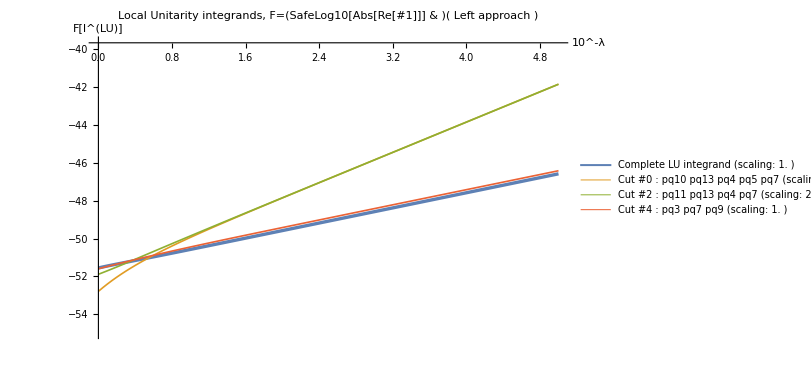
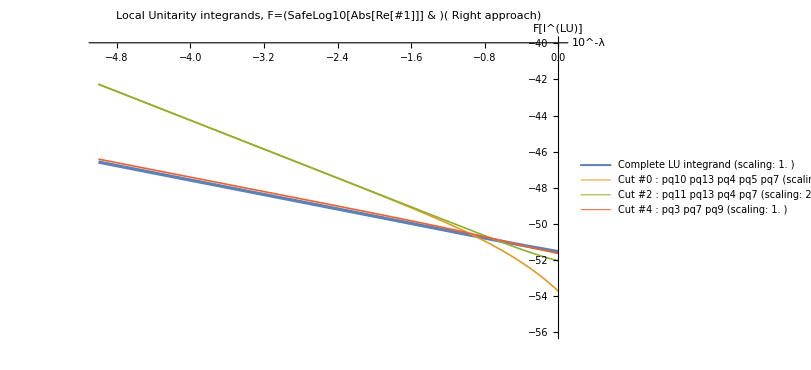
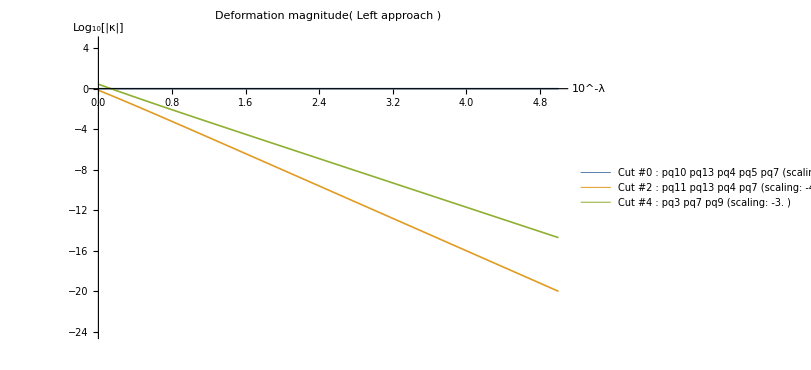
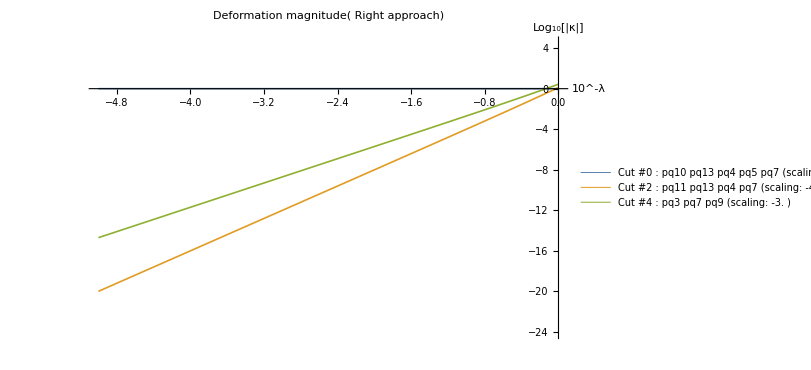
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

### Study of approach of (intersections of) thresholds

We can display the supergraph

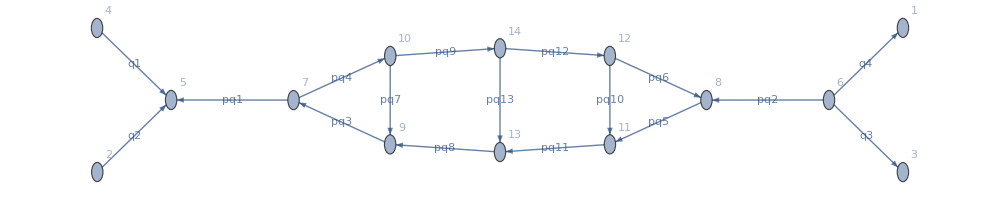

```mathematica
GetSuperGraph[SGYAMLinfo,ShowVertexLabels->Automatic,Size->1000]
```

And all of its LMBs, of which we show here the first twelve

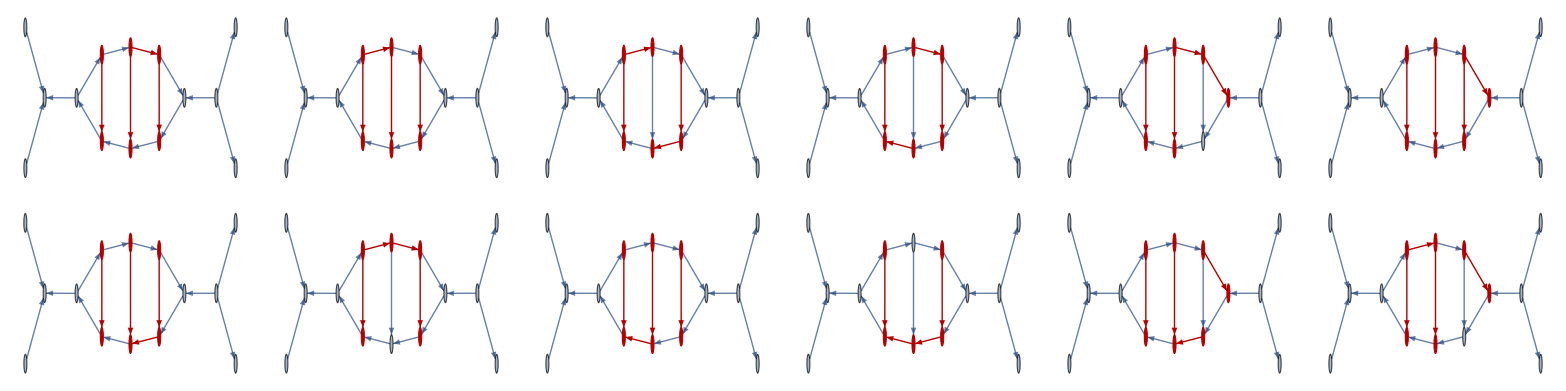

```mathematica
Table[HighlightGraph[GetSuperGraph[SGYAMLinfo],lmb],{lmb, GenerateAllLMBs[SGYAMLinfo]⟦;;12⟧}]//Multicolumn[#,6]&
```

We can automatically generate all E-surfaces (the only slow part is finding whether or not points exists on them)

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
```

And display them:

All 16 s-channel E-surfaces:

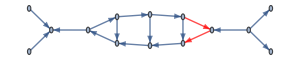
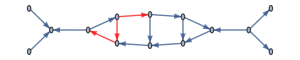
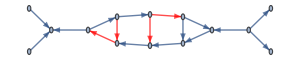
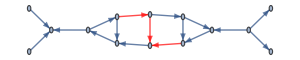
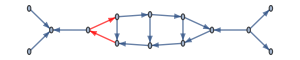
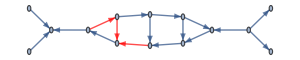
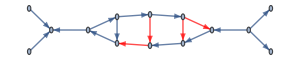
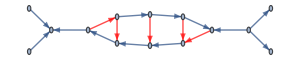
ID 1: | -Graphics- | ID 5: | -Graphics- | ID 9: | -Graphics- | ID 13: | -Graphics- | 
ID 2: | -Graphics- | ID 6: | -Graphics- | ID 10: | -Graphics- | ID 14: | -Graphics- | 
ID 3: | -Graphics- | ID 7: | -Graphics- | ID 11: | -Graphics- | ID 15: | -Graphics- | 
ID 4: | -Graphics- | ID 8: | -Graphics- | ID 12: | -Graphics- | ID 16: | -Graphics- |

All 12 soft E-surfaces:

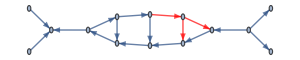
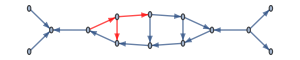
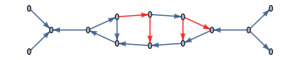
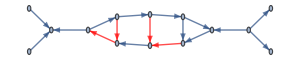
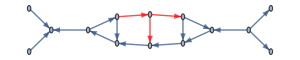
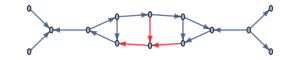
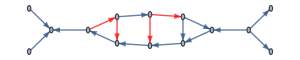
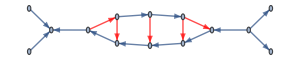
ID 1: | -Graphics- | ID 4: | -Graphics- | ID 7: | -Graphics- | ID 10: | -Graphics- | 
ID 2: | -Graphics- | ID 5: | -Graphics- | ID 8: | -Graphics- | ID 11: | -Graphics- | 
ID 3: | -Graphics- | ID 6: | -Graphics- | ID 9: | -Graphics- | ID 12: | -Graphics- |

All 26 internal E-surfaces:

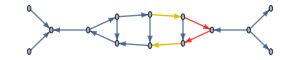
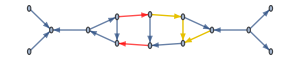
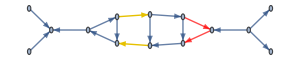
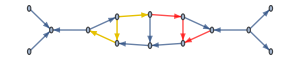
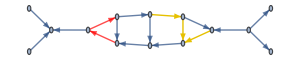
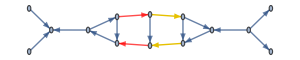
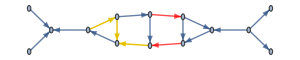
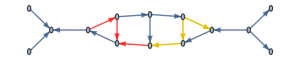
ID 1: | -Graphics- | ID 7: | -Graphics- | ID 13: | -Graphics- | ID 19: | -Graphics- | ID 25: | -Graphics-
ID 2: | -Graphics- | ID 8: | -Graphics- | ID 14: | -Graphics- | ID 20: | -Graphics- | ID 26: | -Graphics-
ID 3: | -Graphics- | ID 9: | -Graphics- | ID 15: | -Graphics- | ID 21: | -Graphics- | 
ID 4: | -Graphics- | ID 10: | -Graphics- | ID 16: | -Graphics- | ID 22: | -Graphics- | 
ID 5: | -Graphics- | ID 11: | -Graphics- | ID 17: | -Graphics- | ID 23: | -Graphics- | 
ID 6: | -Graphics- | ID 12: | -Graphics- | ID 18: | -Graphics- | ID 24: | -Graphics- |

All 30 composite E-surfaces:

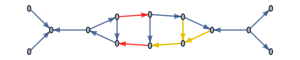
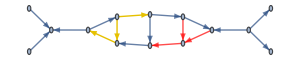
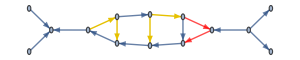
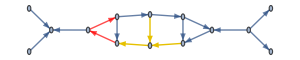
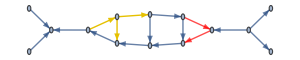
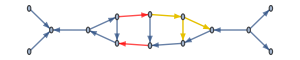
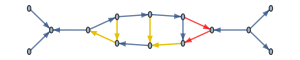
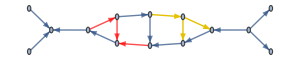
ID 1: | -Graphics- | ID 7: | -Graphics- | ID 13: | -Graphics- | ID 19: | -Graphics- | ID 25: | -Graphics-
ID 2: | -Graphics- | ID 8: | -Graphics- | ID 14: | -Graphics- | ID 20: | -Graphics- | ID 26: | -Graphics-
ID 3: | -Graphics- | ID 9: | -Graphics- | ID 15: | -Graphics- | ID 21: | -Graphics- | ID 27: | -Graphics-
ID 4: | -Graphics- | ID 10: | -Graphics- | ID 16: | -Graphics- | ID 22: | -Graphics- | ID 28: | -Graphics-
ID 5: | -Graphics- | ID 11: | -Graphics- | ID 17: | -Graphics- | ID 23: | -Graphics- | ID 29: | -Graphics-
ID 6: | -Graphics- | ID 12: | -Graphics- | ID 18: | -Graphics- | ID 24: | -Graphics- | ID 30: | -Graphics-

```mathematica
DisplayESurfaces[SGYAMLinfo,allESurfaces,Size->300,Colors->{Red}]
```

Or just one particular one

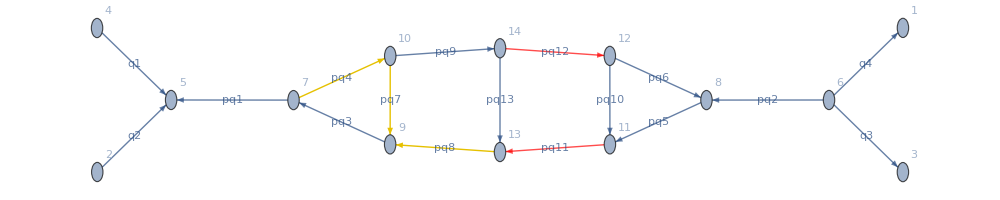

```mathematica
DisplayESurface[SGYAMLinfo,allESurfaces["internal"]⟦8⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

And access a wealth of information about each, e.g.:

```mathematica
MyDataset[allESurfaces["internal"]⟦8⟧]
```

We can build a helper association to directly access Cutkosky cut E-surfaces.

```mathematica
CutkoskyEsurfaces=Association[Table[es["OutgoingEdges"]->es,{es,allESurfaces["s-channel"]}]];
```

And easily find a point on (multiple) E-surfaces as follows:

```mathematica
aPointToExplore=FindPointOnEsurfaces[{CutkoskyEsurfaces[{"pq3","pq7","pq9"}],CutkoskyEsurfaces[{"pq11","pq12"}],CutkoskyEsurfaces[{"pq5","pq6"}]},SGYAMLinfo,NoDeformationHyperparams,DEBUG->False,AcceptThreshold->10^-25]
```

<|pq4→{0.748698076509614778096305,188.5462339045764623364008,-96.31191404047328318224088},pq7→{-22.80762598441086201094969,-119.022908250074953658373,200.0212201705006127852929},pq10→{-60.88859303925227122362449,76.13077927795284010713445,96.52516039899613526165371},pq13→{104.2369245441488449475185,-76.79846975737861477410443,-39.77284964083868346565634}|>

And we can verify that it is indeed located on these three E-surfaces

```mathematica
MyDataset[Association[Table[e->CutkoskyEsurfaces[e]["Eq"]/.GenerateLoopMomenta[SGYAMLinfo,moms->aPointToExplore],{e,Keys[CutkoskyEsurfaces]}]]]
```

Look at all momenta for this configuration:

```mathematica
ComputeAllMomenta[aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

Evaluate the LU expression on it, first without E-surface analysis:

```mathematica
MyDataset[EvaluatePoint[HookWithDeformation,aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1
]]
```

And then including the E-surface analysis

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
```

```mathematica
MyDataset[evaluationWithEsurfaceAnalysis]
```

And now with more detailed info about the E-surface analysis

```mathematica
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel","soft"}];
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

--------------------------------------------------

Analysis of soft E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

We can now approach this point automatically in a double-sided fashion with:

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,aPointToExplore,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

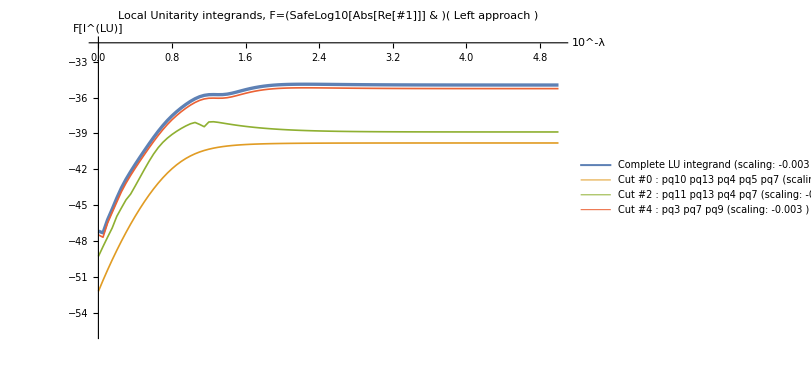
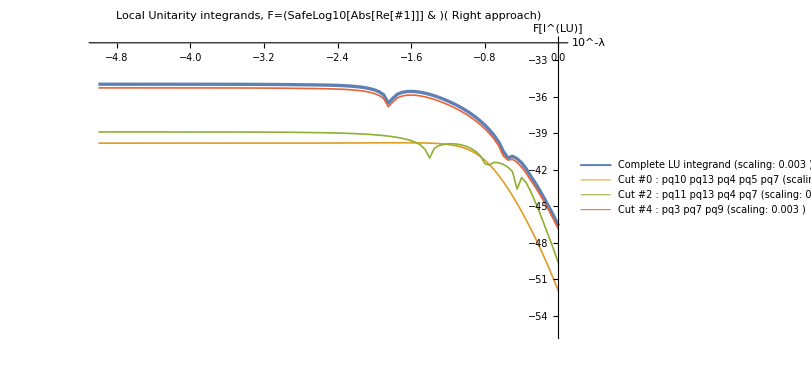
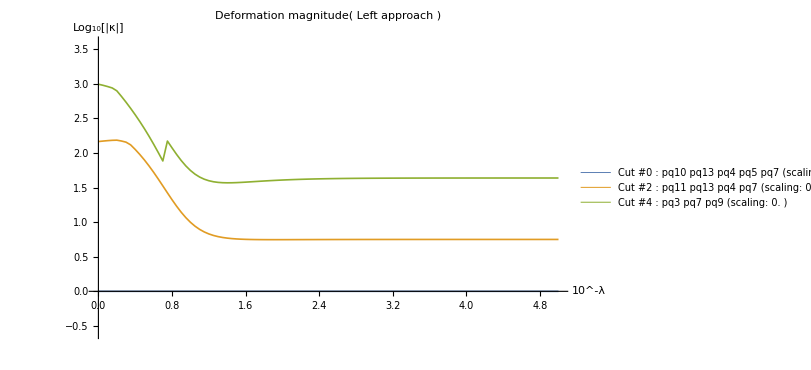
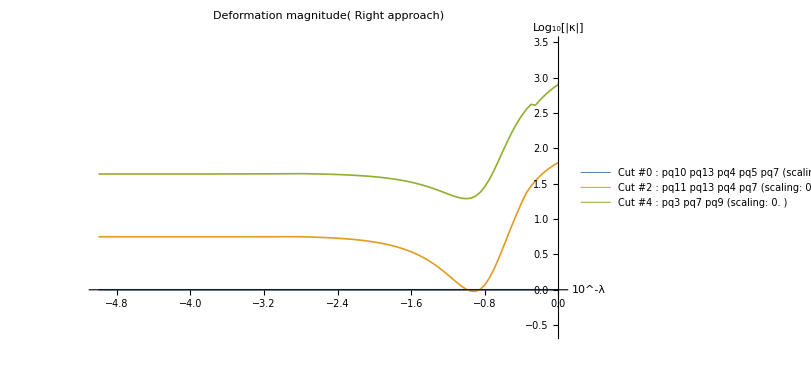
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

But it sometimes better to not look in Log Log plot and study separately the real and imaginary part of the integrand

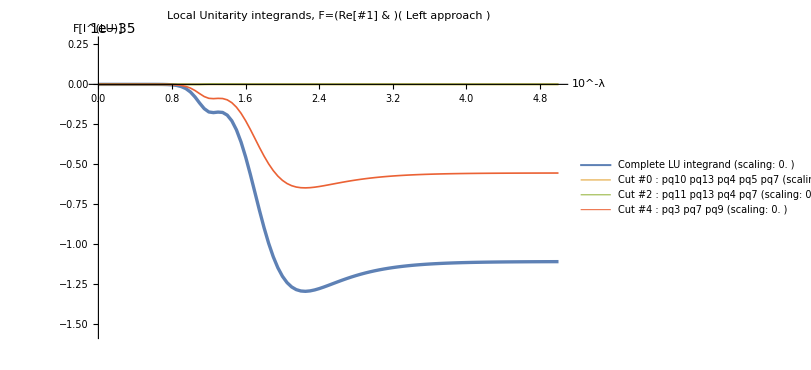
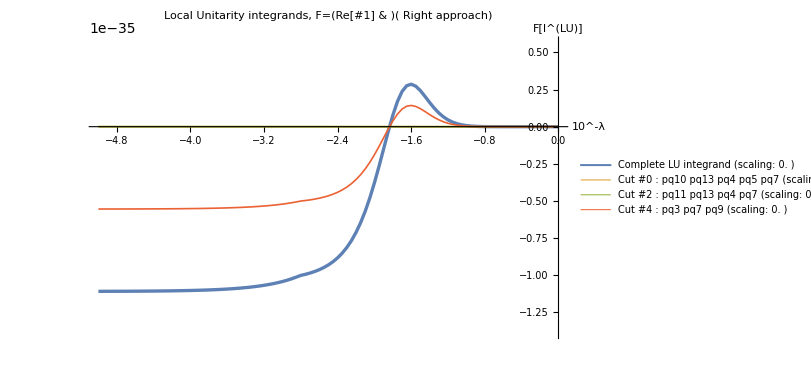
-Graphics- | -Graphics-

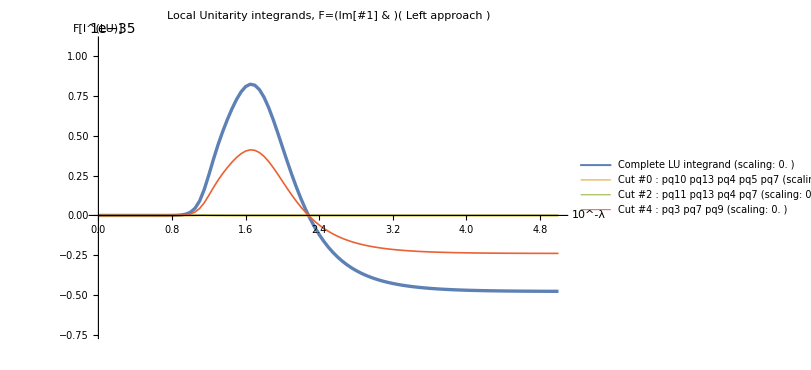
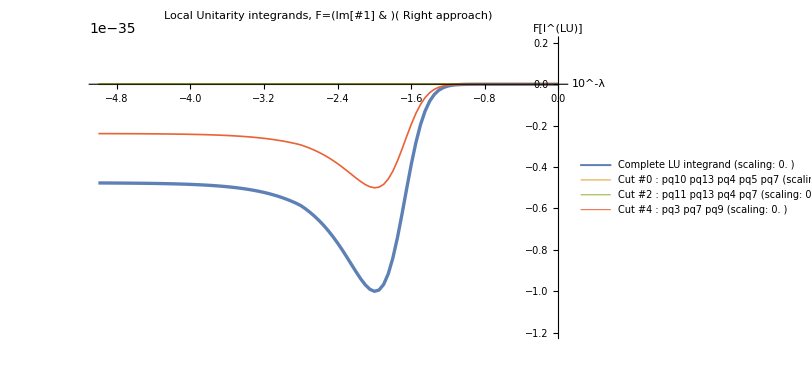
-Graphics- | -Graphics-

```mathematica
Grid[{DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(Re[#]&)]⟦1⟧}]
Grid[{DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(Im[#]&)]⟦1⟧}]
```

And one can bypass the double-sided study and just directly look at a single approach

```mathematica
RefreshHooks[];
ApproachRawData=AnalyzeApproach[HookWithDeformation,aPointToExplore,SGYAMLinfo,WithDeformationHyperparams,NPoints->300,Seed->1, LambdaMax->5.,LambdaMin->0,ApproachSide->-1];
```

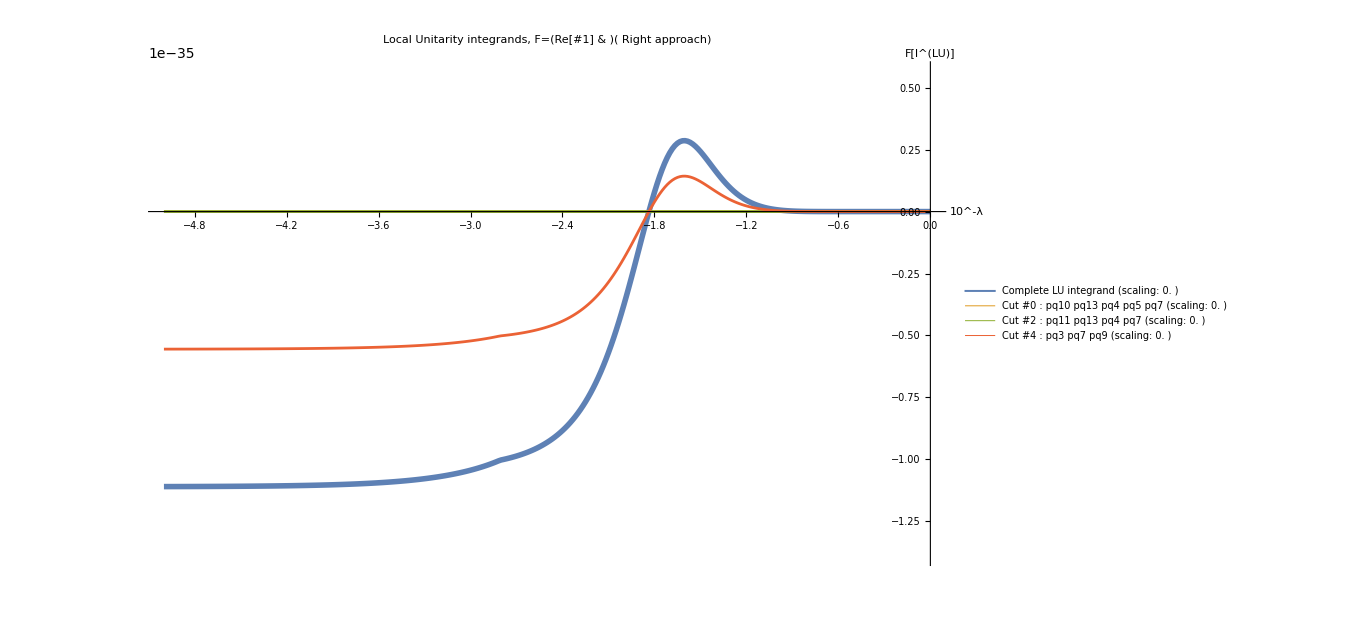
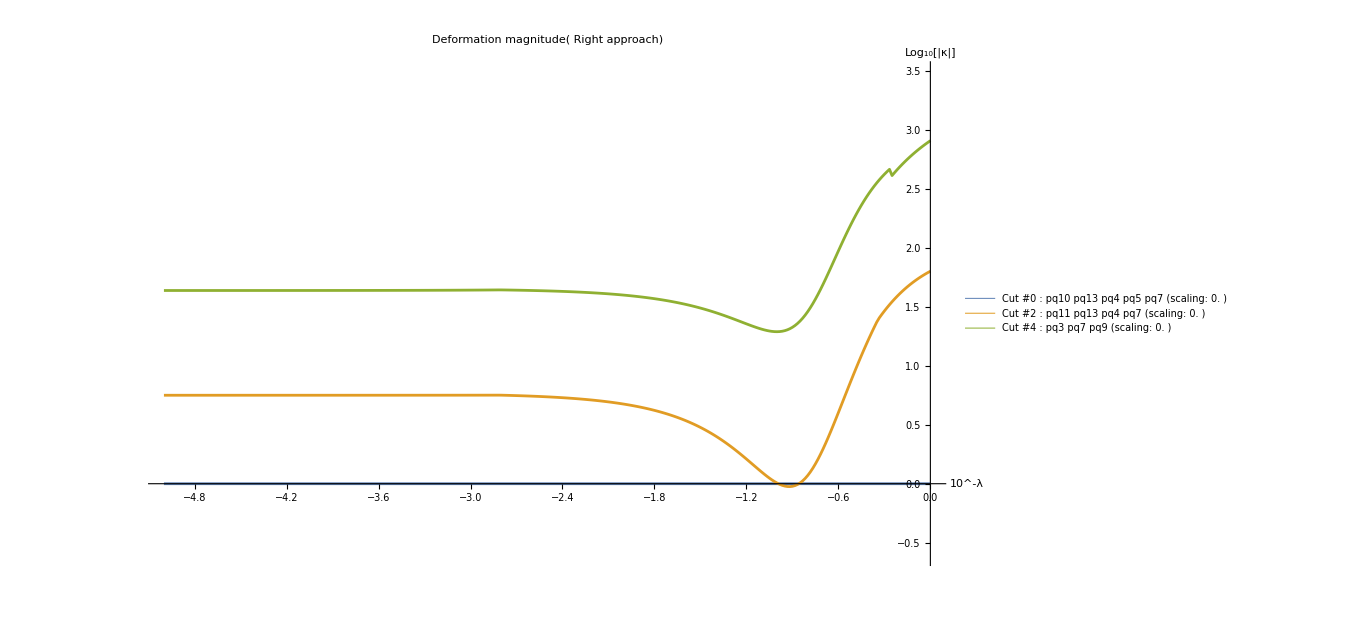

```mathematica
Grid[MonitorApproachResult[ApproachRawData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},ApproachSide->-1,IntegrandToPlot->(Re[#]&)]]
```

### Cross-checking YAML E-surfaces

```mathematica
allYAMLEsurfaces=ImportEsurfacesFromYaml[SGYAMLinfo,NoDeformationHyperparams,GenerateExamplePoints->False,EsurfID->None(*{5,1,2,11}*)];
```

```mathematica
YAMLEsurfacesMap=Association[Table[esurf⟦"id"⟧->esurf,{esurf,allYAMLEsurfaces["YAML"]}]];
```

One can look at all E-surfaces imported this way

All 26 YAML E-surfaces:

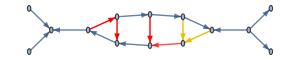
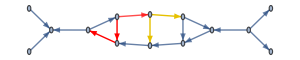
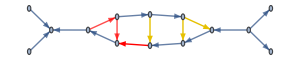
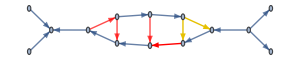
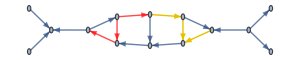
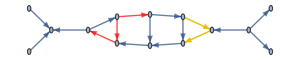
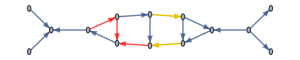
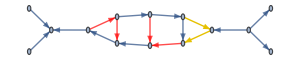
ID #1 ({3, 1, 2, 1}): | -Graphics- | ID #8 ({5, 1, 2, 2}): | -Graphics- | ID #15 ({5, 1, 2, 9}): | -Graphics- | ID #22 ({6, 1, 2, 6}): | -Graphics-
ID #2 ({3, 1, 2, 2}): | -Graphics- | ID #9 ({5, 1, 2, 3}): | -Graphics- | ID #16 ({5, 1, 2, 10}): | -Graphics- | ID #23 ({6, 1, 2, 7}): | -Graphics-
ID #3 ({3, 1, 2, 3}): | -Graphics- | ID #10 ({5, 1, 2, 4}): | -Graphics- | ID #17 ({6, 1, 2, 1}): | -Graphics- | ID #24 ({6, 1, 2, 8}): | -Graphics-
ID #4 ({4, 1, 2, 1}): | -Graphics- | ID #11 ({5, 1, 2, 5}): | -Graphics- | ID #18 ({6, 1, 2, 2}): | -Graphics- | ID #25 ({6, 1, 2, 9}): | -Graphics-
ID #5 ({4, 1, 2, 2}): | -Graphics- | ID #12 ({5, 1, 2, 6}): | -Graphics- | ID #19 ({6, 1, 2, 3}): | -Graphics- | ID #26 ({6, 1, 2, 10}): | -Graphics-
ID #6 ({4, 1, 2, 3}): | -Graphics- | ID #13 ({5, 1, 2, 7}): | -Graphics- | ID #20 ({6, 1, 2, 4}): | -Graphics- | 
ID #7 ({5, 1, 2, 1}): | -Graphics- | ID #14 ({5, 1, 2, 8}): | -Graphics- | ID #21 ({6, 1, 2, 5}): | -Graphics- |

```mathematica
DisplayESurfaces[SGYAMLinfo,allYAMLEsurfaces,Colors->{Red},nCols->4]
```

```mathematica
DisplayESurfaces[SGYAMLinfo,allESurfaces,Colors->{Red},nCols->4]
```

All 16 s-channel E-surfaces:

ID 1: | -Graphics- | ID 5: | -Graphics- | ID 9: | -Graphics- | ID 13: | -Graphics-
ID 2: | -Graphics- | ID 6: | -Graphics- | ID 10: | -Graphics- | ID 14: | -Graphics-
ID 3: | -Graphics- | ID 7: | -Graphics- | ID 11: | -Graphics- | ID 15: | -Graphics-
ID 4: | -Graphics- | ID 8: | -Graphics- | ID 12: | -Graphics- | ID 16: | -Graphics-

All 12 soft E-surfaces:

ID 1: | -Graphics- | ID 4: | -Graphics- | ID 7: | -Graphics- | ID 10: | -Graphics-
ID 2: | -Graphics- | ID 5: | -Graphics- | ID 8: | -Graphics- | ID 11: | -Graphics-
ID 3: | -Graphics- | ID 6: | -Graphics- | ID 9: | -Graphics- | ID 12: | -Graphics-

All 26 internal E-surfaces:

ID 1: | -Graphics- | ID 8: | -Graphics- | ID 15: | -Graphics- | ID 22: | -Graphics-
ID 2: | -Graphics- | ID 9: | -Graphics- | ID 16: | -Graphics- | ID 23: | -Graphics-
ID 3: | -Graphics- | ID 10: | -Graphics- | ID 17: | -Graphics- | ID 24: | -Graphics-
ID 4: | -Graphics- | ID 11: | -Graphics- | ID 18: | -Graphics- | ID 25: | -Graphics-
ID 5: | -Graphics- | ID 12: | -Graphics- | ID 19: | -Graphics- | ID 26: | -Graphics-
ID 6: | -Graphics- | ID 13: | -Graphics- | ID 20: | -Graphics- | 
ID 7: | -Graphics- | ID 14: | -Graphics- | ID 21: | -Graphics- |

All 30 composite E-surfaces:

ID 1: | -Graphics- | ID 9: | -Graphics- | ID 17: | -Graphics- | ID 25: | -Graphics-
ID 2: | -Graphics- | ID 10: | -Graphics- | ID 18: | -Graphics- | ID 26: | -Graphics-
ID 3: | -Graphics- | ID 11: | -Graphics- | ID 19: | -Graphics- | ID 27: | -Graphics-
ID 4: | -Graphics- | ID 12: | -Graphics- | ID 20: | -Graphics- | ID 28: | -Graphics-
ID 5: | -Graphics- | ID 13: | -Graphics- | ID 21: | -Graphics- | ID 29: | -Graphics-
ID 6: | -Graphics- | ID 14: | -Graphics- | ID 22: | -Graphics- | ID 30: | -Graphics-
ID 7: | -Graphics- | ID 15: | -Graphics- | ID 23: | -Graphics- | 
ID 8: | -Graphics- | ID 16: | -Graphics- | ID 24: | -Graphics- |

Or one at a time:

```mathematica
DisplayESurface[SGYAMLinfo,allYAMLEsurfaces["YAML"]⟦1⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

-Graphics-

Or one can also look at the YAML raw data for this E-surface:

```mathematica
(SGYAMLinfo["cutkosky_cuts"]⟦ #⟦1⟧ ⟧["diagram_sets"]⟦ #⟦2⟧ ⟧["diagram_info"]⟦ #⟦3⟧ ⟧["thresholds"]⟦ #⟦4⟧ ⟧&)@allYAMLEsurfaces["YAML"]⟦2⟧["id"]
```

<|foci→{2,1},mass_shift→0.,shift_in_lmb_sig→{{-1,1,0,1},{1,1,-1,-1}}|>

And the data generated for it too

```mathematica
Dataset[allYAMLEsurfaces["YAML"]⟦1⟧]
```

Find correspondences with independent generation of these E-surfaces

```mathematica
EsurfMappings=FindMappingOfYAMLEsurfaces[SGYAMLinfo,allYAMLEsurfaces,allESurfaces];
```

Error: Found 0 matches for cutkosky cut 3 (s-channel E-surf #12) with edges {pq11, pq13, pq4, pq7} and soft E-surface with edges {pq10, pq11, pq5}

Error: Found 0 matches for cutkosky cut 3 (s-channel E-surf #12) with edges {pq11, pq13, pq4, pq7} and soft E-surface with edges {pq10, pq13, pq4, pq6, pq7}

Error: Found 0 matches for cutkosky cut 4 (s-channel E-surf #9) with edges {pq12, pq13, pq3, pq7} and soft E-surface with edges {pq10, pq12, pq6}

Error: Found 0 matches for cutkosky cut 4 (s-channel E-surf #9) with edges {pq12, pq13, pq3, pq7} and soft E-surface with edges {pq10, pq13, pq3, pq5, pq7}

Error: Found 0 matches for cutkosky cut 5 (s-channel E-surf #5) with edges {pq3, pq7, pq9} and soft E-surface with edges {pq12, pq13, pq9}

Error: Found 0 matches for cutkosky cut 5 (s-channel E-surf #5) with edges {pq3, pq7, pq9} and soft E-surface with edges {pq10, pq13, pq6, pq9}

Error: Found 0 matches for cutkosky cut 5 (s-channel E-surf #5) with edges {pq3, pq7, pq9} and soft E-surface with edges {pq11, pq13, pq3, pq7}

Error: Found 0 matches for cutkosky cut 5 (s-channel E-surf #5) with edges {pq3, pq7, pq9} and soft E-surface with edges {pq10, pq13, pq3, pq5, pq7}

Error: Found 0 matches for cutkosky cut 6 (s-channel E-surf #6) with edges {pq4, pq7, pq8} and soft E-surface with edges {pq11, pq13, pq8}

Error: Found 0 matches for cutkosky cut 6 (s-channel E-surf #6) with edges {pq4, pq7, pq8} and soft E-surface with edges {pq12, pq13, pq4, pq7}

Error: Found 0 matches for cutkosky cut 6 (s-channel E-surf #6) with edges {pq4, pq7, pq8} and soft E-surface with edges {pq10, pq13, pq5, pq8}

Error: Found 0 matches for cutkosky cut 6 (s-channel E-surf #6) with edges {pq4, pq7, pq8} and soft E-surface with edges {pq10, pq13, pq4, pq6, pq7}

Let’s compare two different representations of the same E-surface thresholds:

```mathematica
EsurfMappings[3][{{"s-channel",12},{"s-channel",4}}]
```

{YAML,{3,1,2,2}}

First as a combination of two thresholds

```mathematica
{DisplayESurface[SGYAMLinfo,allESurfaces["s-channel"]⟦12⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic],
DisplayESurface[SGYAMLinfo,allESurfaces["s-channel"]⟦4⟧,Size->1000,Colors->{Green},ShowVertexLabels->Automatic],
}//Multicolumn[#,2]&
```

-Graphics- | 
-Graphics- |

And then as a YAML amplitude-Esurface

```mathematica
DisplayESurface[SGYAMLinfo,YAMLEsurfacesMap[EsurfMappings[3][{{"s-channel",12},{"s-channel",4}}]⟦2⟧],Size->1000,Colors->{Red,Green},ShowVertexLabels->Automatic]
```

-Graphics-

And finally compare their evaluation of the E-surface equation for particular momenta lying on the corresponding Cutkosky cuts:

```mathematica
failedEqComparisons=CompareEquations[SGYAMLinfo,NoDeformationHyperparams,EsurfMappings,allYAMLEsurfaces,allESurfaces,DEBUG->True,AcceptThreshold->10^-12];
```

Error: could not perform comparison for cutkosky cut 3, s-channel E-surf #12 with edges {pq4, pq7, pq11, pq13} and soft E-surface with edges {pq5, pq11, pq10} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 3, s-channel E-surf #12 with edges {pq4, pq7, pq11, pq13} and soft E-surface with edges {pq4, pq7, pq6, pq10, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 4, s-channel E-surf #9 with edges {pq3, pq7, pq12, pq13} and soft E-surface with edges {pq6, pq10, pq12} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 4, s-channel E-surf #9 with edges {pq3, pq7, pq12, pq13} and soft E-surface with edges {pq5, pq3, pq7, pq10, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 5, s-channel E-surf #5 with edges {pq3, pq7, pq9} and soft E-surface with edges {pq9, pq12, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 5, s-channel E-surf #5 with edges {pq3, pq7, pq9} and soft E-surface with edges {pq9, pq6, pq10, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 5, s-channel E-surf #5 with edges {pq3, pq7, pq9} and soft E-surface with edges {pq3, pq7, pq11, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 5, s-channel E-surf #5 with edges {pq3, pq7, pq9} and soft E-surface with edges {pq5, pq3, pq7, pq10, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 6, s-channel E-surf #6 with edges {pq4, pq7, pq8} and soft E-surface with edges {pq11, pq8, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 6, s-channel E-surf #6 with edges {pq4, pq7, pq8} and soft E-surface with edges {pq4, pq7, pq12, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 6, s-channel E-surf #6 with edges {pq4, pq7, pq8} and soft E-surface with edges {pq5, pq10, pq8, pq13} because the YAML mapped E-surface is missing.

Error: could not perform comparison for cutkosky cut 6, s-channel E-surf #6 with edges {pq4, pq7, pq8} and soft E-surface with edges {pq4, pq7, pq6, pq10, pq13} because the YAML mapped E-surface is missing.

SUCCESS: All 26 equation comparisons are successful.

Notice that this is a non-trivial check because the equations look very different, i.e.:

```mathematica
allESurfaces["s-channel"]⟦4⟧["Eq"]
```

-1000.+√(k3x^2+k3y^2+k3z^2)+√(29929.+(k1x-k2x-k4x)^2+(k1y-k2y-k4y)^2+(k1z-k2z-k4z)^2)+√(29929.+(k1x-k2x-k3x-k4x)^2+(k1y-k2y-k3y-k4y)^2+(k1z-k2z-k3z-k4z)^2)

vs

```mathematica
YAMLEsurfacesMap[{3,1,2,2}]["Eq"]
```

0.-√(29929.+k1x^2+k1y^2+k1z^2)-√(15625.+k2x^2+k2y^2+k2z^2)+√(0.+(0.+k3x)^2+(0.+k3y)^2+(0.+k3z)^2)+√(29929.+(0.+k1x-k2x-k3x-k4x)^2+(0.+k1y-k2y-k3y-k4y)^2+(0.+k1z-k2z-k3z-k4z)^2)-√(k4x^2+k4y^2+k4z^2)

And they match only when evaluated on the Cutkosky cut, i.e. the difference reads:

```mathematica
(allESurfaces["s-channel"]⟦4⟧["Eq"]-YAMLEsurfacesMap[{3,1,2,2}]["Eq"])//Simplify
```

-1000.+√(29929.+k1x^2+k1y^2+k1z^2)+√(15625.+k2x^2+k2y^2+k2z^2)+√(k4x^2+k4y^2+k4z^2)+√(29929.+(-k1x+k2x+k4x)^2+(-k1y+k2y+k4y)^2+(-k1z+k2z+k4z)^2)

Which is exactly the equation of the cutkosky cut, i.e.:

```mathematica
allESurfaces["s-channel"]⟦12⟧["Eq"]
```

-1000.+√(29929.+k1x^2+k1y^2+k1z^2)+√(15625.+k2x^2+k2y^2+k2z^2)+√(29929.+(k1x-k2x-k4x)^2+(k1y-k2y-k4y)^2+(k1z-k2z-k4z)^2)+√(k4x^2+k4y^2+k4z^2)

```mathematica
allESurfaces["s-channel"]⟦12⟧["Eq"]-(allESurfaces["s-channel"]⟦4⟧["Eq"]-YAMLEsurfacesMap[{3,1,2,2}]["Eq"])//Simplify
```

0

### Analysis of a max weight point

We can automatically map the xs variable to the point in the sampling basis active at run time (use all integration channels if multichanneling was enabled

```mathematica
maxWgtPoint=MapFromXs[HookWithDeformation,
{0.849593720848453,0.24429579449322847,0.6402108135745326,0.8560665730509239,0.7384368123709596,0.36724149939496614,0.14036138814108864,0.16762193841514772,0.6144196438490055,0.34658379011798746,0.16176951799648479,0.7382519129987205}, 
SGYAMLinfo,NoDeformationHyperparams,basis->{"pq10", "pq13", "pq7", "pq5"}]
```

<|pq4→{102.169,234.105,294.913},pq7→{78.6458,138.126,37.3648},pq10→{194.287,5418.53,1584.01},pq13→{-416.242,-5719.04,-1579.2}|>

And now run the standard set of analysis tools onto it

```mathematica
ComputeAllMomenta[maxWgtPoint,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,maxWgtPoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
```

```mathematica
Dataset[evaluationWithEsurfaceAnalysis][All,"Rescaling"]
```

```mathematica
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel"}];
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,maxWgtPoint,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

-Graphics- | -Graphics-
-Graphics- | -Graphics-

### Multi-channeled evaluation dissection

Here is a multi-channeled max weight point:

```mathematica
xsPointForMultiChannelAnalysis={0.07209142507053912,0.7211560788564384,0.48690233076922596,
0.0042818577494472265,0.2789711025543511,0.8129998685326427,
0.05190556729212403,0.9428516994230449,0.7796795438043773,
0.15656883548945189,0.8171080858446658,0.2982940352521837};
```

We can evaluate it directly using the API

```mathematica
RefreshHooks[];
RFM$EvaluateIntegrand[HookRunConfig,xsPointForMultiChannelAnalysis]
```

8.7804×10^-6+0.00010524 ⅈ

Or dissect it with “MultiChannelPointAnalyzer”, beware however that one must supply a Hook here which has loaded a yaml that does *not* use multichanneling, since we will be using non-multichanneled evaluations to dissect the evaluation

```mathematica
RefreshHooks[];
multiChannelAnalysis=MultiChannelPointAnalyzer[HookWithDeformation,SGYAMLinfo,RunConfigHyperparams,xsPointForMultiChannelAnalysis,Esurfaces->allYAMLEsurfaces,DEBUG->False];
```

And we recover the multi-channeled evaluation above, and gather additional stats

```mathematica
MyDataset[multiChannelAnalysis["statistics"]]
```

One can then look at the result from each channel, sorted from most to least relevant

```mathematica
MyDataset[multiChannelAnalysis["summary"]]
```

One can then look at details of the evaluation for each channel and each Cutkosky cut:

```mathematica
MyDataset[multiChannelAnalysis["full"][{"optimised",0}][3]]
```

And conveniently display E-surface evaluations:

```mathematica
DisplayEvaluationEsurf[multiChannelAnalysis["full"][{"optimised",0}],SGYAMLinfo]
```

--------------------------------------------------

Analysis of YAML E-surfaces:

--------------------------------------------------

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #3 | {pq12,pq13,pq3,pq7}
 | Cut #5 | {pq4,pq7,pq8}

--------------------------------------------------

Analysis of UV E-surfaces:

--------------------------------------------------

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #3 | {pq12,pq13,pq3,pq7}
 | Cut #5 | {pq4,pq7,pq8}

### Testing deformation on (intersections of) E-surfaces

```mathematica
allIntersections=FindYAMLEsurfaceIntersections[allYAMLEsurfaces,allCutkoskyEsurfaces,SGYAMLinfo,NoDeformationHyperparams,MaxNEsurfaces->2];
```

Error: could not find Cutkoksy cut E-surface for cut #0 and edges {pq10, pq13, pq4, pq5, pq7}

Error: could not find Cutkoksy cut E-surface for cut #1 and edges {pq10, pq13, pq3, pq6, pq7}

Error: could not find Cutkoksy cut E-surface for cut #2 and edges {pq11, pq13, pq4, pq7}

Error: could not find Cutkoksy cut E-surface for cut #3 and edges {pq12, pq13, pq3, pq7}

```mathematica
RefreshHooks[];
intersectionAnalysisResults=AnalyzeEsurfaceIntersections[
HookWithoutDeformation,HookWithDeformation,allIntersections,allYAMLEsurfaces,allCutkoskyEsurfaces,SGYAMLinfo,NoDeformationHyperparams,Seed->Automatic
];
```

Keys::invrl: The argument Association[«1»] is not a valid Association or a list of rules.

Do::iterb: Iterator … does not have appropriate bounds.

All 0 intersections test passed.

And one can look at individual results then:

```mathematica
MyDataset[intersectionAnalysisResults["details"][{4,1,{{"YAML",{4, 1, 2, 2}}}}]["summary"]]
```

And the particular intersection point considered

```mathematica
MyDataset[intersectionAnalysisResults["details"][{4,1,{{"YAML",{4, 1, 2, 2}}}}]["details"]["intersection_point"]]
```

And even the evolution of certain quantitities during the approach

```mathematica
MyDataset[Table[{evals⟦1⟧,evals⟦2⟧[4]["Res"]},{evals,intersectionAnalysisResults["details"][{4,1,{{"YAML",{4, 1, 2, 2}}}}]["details"]["no_deformation_evaluations"]}]]
```

Table::iterb: Iterator {evals,Missing[KeyAbsent,{4,1,{{YAML,{4,1,2,2}}}}][details][no_deformation_evaluations]} does not have appropriate bounds.

### Workspace

Put there experiments